# SurfAnal 13 for freeform surface from OGP and gantry data

2015.07.14 - Added ITL VIEW data format read in.
2014.12.03  -  Cleaned up the trim points section. Now use histogram view to set the z-trim limits.
2013.08.07 ver 13 - Rename the working arrays to clarify function.
2013.07.19 ver 12b - Added Chebyshev polynomial fit. Could not add display of fit coefficients vs order of the polynomial. Use MathGroup solutions to Hold and Release question.
2013.06.28 ver. 11 - Added section to read in separate REF cal file, clean it up, fit to a polynomial and then subtract the fit from the SUT data. This corrects for OGP systematic error.
2012.05.21 ver. 10a - Changed “sparse” variable name to “cloud”. Modifed triplet text input to handle 4 or 5 or more numbers in a record. THen extract the XYZ values and continue.
2012.05.15 - Cleaned up OGP data input. Added BoxWhiskerPlot and better labeling. Only convert OGP z-values to microns.
2011.01.21 - Added IGES format for OGP files. Convert OGP triplets into integers (microns).
2010.09.27 - Modified for Quick Surface Scan data format.
2010.02.25 - Added Lanczos differentiator in 2D from Hamming book. Reduces high freq noise.
2009.12.15 ver. 9 - modified to handle variable row and column length for OGP data.
2009.06.22  ver.8 - Added general input file section for unknown formats. As shown for output from David's Keyence gantry program.
2008.05.07  ver. 7 -  Added function to plot discontinuous surfaces correctly showing blank regions. Requires setting bad ponts to imaginary value.
2008.03  Does GEM foil analysis
2008.02.18  Add H2S routines.
2007.05.19 ver.3 - Changed names of variables. Added tick function to scale index values into physical units.

2007.04.14
ver. 01 - Combines KeyDetectSurf 05  and SurfaceFlatness with bad points fixer.

Reads in Keyence area data from LabView file.

2007.04.01 Generalized the 2D surface fit function to any order in x&y.2006.12.20 Added Bad Data Point finder.

2007.02.18 -  Generalize surface fit to any order

PZT  2006 March 15 - KeyDetectSurf ver. 01

#### Reads in Keyence area data from LabView file.

Data file is structured as a matrix of points. Entries are triplets of x,y,z values. Data is separated into scans. Data for each scan is arranged sequentially as row 1, row 2, etc. So the file is a list of scans, each scan is a list of rows, each row is a list of data triplets.

Note that the file is structured so that the x-value varies fastest. Triplets are arranged in rows in the file with the x-value changing fastest. One complete x-scan comprises a single row of data at a single y-value. The index for the x-value is the column identifier in the array,  the y-position is  the row identifier.

Need to strip off the z values and do statistics on them, keeping track of what x-y coord is of each z-value. THis is done by partitioning appropriately at the right time in the analysis.

Execute next statement first. It causes all of the initialization cells to be executed.

```mathematica
Button["Run Initialization first",FrontEndExecute[FrontEndToken["EvaluateInitialization"]]]
```

Run Initialization first

## 1. Initialize

Data and time of last saved modification. This is an Initialization cell that executes automatically whenever the nb is opened.

```mathematica
nb=EvaluationNotebook[]
```

st62d_shm15FrontEndObject[LinkObject["st62d_shm", 3, 1]]15SurfAnal 13 freeform cloud.nb/Users/takacs/ Peter work f/Mathematica work/Surface analysis/SurfAnal 13 freeform cloud.nb

```mathematica
DateString["FileModificationTime"/.NotebookInformation[],TimeZone->0]
```

Tue 14 Jul 2015 22:02:07

```mathematica
Off[General::"spell1"]
(*<<"BarCharts`";<<"Histograms`";<<"PieCharts`"
<<"LinearRegression`"*)
```

```mathematica
<<ComputationalGeometry`
```

```mathematica
$SystemID
```

MacOSX-x86-64

```mathematica
$OperatingSystem
```

MacOSX

```mathematica
SetOptions[ListPlot3D,BaseStyle->Directive[Bold,FontFamily->"Arial",FontSize->10]];
```

```mathematica
SetOptions[Histogram,BaseStyle->Directive[Bold,FontFamily->"Arial",FontSize->10]];
```

```mathematica
SetOptions[ListPointPlot3D,BaseStyle->Directive[Bold,FontFamily->"Arial",FontSize->10]];
```

```mathematica
SetOptions[ListContourPlot,BaseStyle->Directive[Bold,FontFamily->"Arial",FontSize->10]];
```

```mathematica
SetOptions[Histogram,BaseStyle->Directive[Bold,FontFamily->"Arial",FontSize->10]];
```

#### Conversion factors to meters for numbers in the indicated units:

```mathematica
mm=10.^-3;
micron=10.^-6;
µm=10.^-6;
nm=10.^-9;
Angstroms=10.^-10;
micronsToAngstroms=10^4;
```

```mathematica
(* MemoryInUse[] *)
(* Share[] *)
```

## 2. Define statistical functions for profile data.

MAKE SURE THE FOURIER OPTIONS ARE SET CORRECTLY EACH TIME THE FT IS DONE.

Define the biased stddev functiion. The built in StdDev fcn has n-1 in the denom. Change it to n.

Now compute std dev in different ways: The default StandardDeviation is the unbiased version, with n-1 in the denominator.

```mathematica
sdevBiased=.
```

```mathematica
sdevUnB[in_]:=N[StandardDeviation[in]]
```

```mathematica
sdevBiased[in_]:=StandardDeviation[in]Sqrt[(Length[in]-1)/Length[in]]
```

```mathematica
rmsBias[in_]:=Sqrt[Plus@@(in^2)/Length[in]]
```

Next is the RMS. Sum the squares, divide by N and then take the root. (Root of the Mean Square)

```mathematica
rmsrawbiased=.;
```

```mathematica
rms[in_]:=N[√((Plus@@((in)^2))/Length[in])]
```

See that one must subtract the mean from the input data first, before squaring, in order to compute the standard deviation correctly.

```mathematica
sdevBruteUnBiased[in_]:=N[√((Plus@@((in-Mean[in])^2))/(Length[in]-1))]
```

```mathematica
detrend[anylist_,order_Integer]:=Block[{npts,xlist,fitlist,x},
If[
order>=0,
xlist=Table[x^i,{i,0,order}];
		npts=Length[anylist];
		func=Fit[anylist,xlist,x];
		fitlist={};
		Do[AppendTo[fitlist,func],{x,1,npts}];
		Return[anylist-fitlist],
Return[anylist]
]
]
```

#### Define a RMS function to compute rms from PSD data. Input arguments are: psd=name of PSD list; ntot=total points in source profile; delx= physical increment value for each data point step; lo and hi = index value in the PSD list.

```mathematica
psd1[in_,delx_]:=(SetOptions[Fourier,FourierParameters->{1,1}];
nPts=Length[in];
FTwork=Fourier[in];
psd2side=(2 delx/nPts) Abs[FTwork]^2;
psd1side=Drop[psd2side,-Floor[(nPts-1)/2]];
(*Apply bookkeeping factors to end terms*)
psd1side[[1]]=psd1side[[1]]/2; 
If[EvenQ[nPts],psd1side[[-1]]=psd1side[[-1]]/2,Null];
psd1side
)
```

```mathematica
npts=.
```

```mathematica
test11={1,2,3,4,5,6,7,8,9,10,11};
```

```mathematica
psd1[test11,1.]
```

{396.,69.2929,18.8168,9.62957,6.64709,5.6137}

```mathematica
nPts
```

11

```mathematica
Length[psd2side]
```

11

#### Define a RMS function to compute rms from PSD data. Input arguments are: psd=name of PSD list; ntot=total points in source profile; delx= physical increment value for each data point step; lo and hi = index value in the PSD list. NOTE: Need to know the length of the input z-vector for the ntot number. Can't get it from the length of the psd list. It should be the length of the psd2side list if this corresponds to the input psd list.

```mathematica
rmspsdIDX[psd_,nztot_,delx_,lo_,hi_]:=(rmsval=N[√((Plus@@Take[psd,{lo,hi}])/(nztot delx))];Print["RMS over index range [",lo,",",hi,"] = ",rmsval])
```

```mathematica
rmspsd[psd_,nztot_,delx_,lo_,hi_]:=N[√((Plus@@Take[psd,{lo,hi}])/(nztot delx))];
```

Now generalize the variance calculation to apply to zero-padded data to give the same result as for the original data set. Need to boost up each term separately.

```mathematica
varGen[anylist_,beforeLen_,afterLen_]:=N[sfac=afterLen/beforeLen;(sfac Plus@@(anylist^2))/afterLen-sfac^2 ((Plus@@anylist)/afterLen)^2]
```

```mathematica
sdevGen=√varGen[worklist,nbefore,nafter]
```

√(-(1. worklist^2)/nbefore^2+(2.+worklist)/nbefore)

#### Add a point digitizer to a plot. Results are put into vector "res".

```mathematica
locatePts[plotname_]:=
Block[ {}, 
res = {}; 
Dynamic[res]; 
  EventHandler[ 
         plotname, {"MouseDown" :>( AppendTo[res, MousePosition["Graphics"]])} 
        ] ]
```

#### The following tick function rescales the axes labels from the default [xmin, xmax] range by offsetting the starting point by b and scaling the tick value by m. Note that you need to specify the AxesOrigin in terms of the unshifted function.

```mathematica
$TextStyle={FontFamily->Arial,FontSize->10}
```

{FontFamily→Arial,FontSize→10}

```mathematica
Style[PlotLabel,DefaultOptions->{FontFamily->Arial}]
```

PlotLabel

```mathematica
tickf[min_,max_,m_,b_,step_]:= Table[{i,m (i-b)},{i,min,max,step}]
```

## 3. Enter path to desired file here. Default directory is set to the parent directory of this file.

```mathematica
"/Users/takacs/ Peter work f/Mathematica work/Surface analysis/test folder/Dummy text.txt"
```

```mathematica
"/Users/takacs/ Peter work f/Data files/OGP data/grid.txt"
```

```mathematica
"/Users/takacs/ Peter work f/Data files/OGP data/more_grid_resaved.xls"
```

```mathematica
"/Users/takacs/ Peter work f/Data files/OGP data/more_grid.xls"
```

```mathematica
"/Users/takacs/ Peter work f/Data files/OGP data/All data/More Data/lines_circles.DAT"
```

```mathematica
"/Users/takacs/ Peter work f/Data files/OGP data/All data/More Data/lines_circles_two.txt"
```

```mathematica
"/Users/takacs/ Peter work f/Data files/OGP data/All data/Optical Flat/Optical_Flat_two.txt"
```

```mathematica
"/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/misc data & docs/OGP from AZ/CCD1.DAT"
```

```mathematica
"/Users/takacs/ Peter work f/Data files/Data 2000 and after/Siddons FloatGlass#7/Schott#07_11.DAT"
```

```mathematica
"/Users/takacs/ Peter work f/Data files/Data 2000 and after/Siddons FloatGlass#7/Schott#07_12.DAT"
```

```mathematica
"/Users/takacs/ Peter work f/Data files/Data 2000 and after/Siddons FloatGlass#7/07_Yfastaxis_01.DAT"
```

```mathematica
"/Users/takacs/ Peter work f/Data files/Data 2000 and after/Siddons FloatGlass#7/07_Yfastaxis_02.DAT"
```

```mathematica
"/Users/takacs/ Peter work f/Data files/Data 2000 and after/Siddons FloatGlass#7/07_Yfastaxis_03.DAT"
```

```mathematica
"/Users/takacs/ Peter work f/Data files/Data 2000 and after/Siddons FloatGlass#7/25_Yfastaxis_01.DAT"
```

```mathematica
"/Users/takacs/ Peter work f/Data files/Data 2000 and after/Siddons FloatGlass#7/25_Yfastaxis_02_20.DAT"
```

```mathematica
"/Users/takacs/Desktop/tile.IGS"
```

```mathematica
"/Users/takacs/ Peter work f/Misc/misc stuff/Tile problem 2011/tile.IGS"
```

```mathematica
"/Users/takacs/ Peter work f/Misc/misc stuff/Tile problem 2011/tile02.IGS"
```

```mathematica
"/Users/takacs/ Peter work f/Data files/Data 2000 and after/LSST raft/4sensor raft 110216.DAT"
```

```mathematica
"/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/111-01 e2v full size/M111-01_01.asc"
```

```mathematica
"/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/Flatness_raft/jhaupt/RaftOnly/3-16-11/RaftOnly3-16-11.DAT"
```

```mathematica
"/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/112-01 e2V#035/CCD250#035_01.dat"
```

```mathematica
"/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/112-02 e2V#034/CCD250#034_01.asc"
```

```mathematica
"/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/106-07/106-07 flatness/N100223_02stitch20x9 106-07.asc"
```

```mathematica
"/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/110_01_e2V mech sample 09/e2V MS09 42mmX42mm stitch.asc"
```

```mathematica
"/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/110_02_e2V mech samp 14/e2V MS14 42mmX42mm.asc"
```

```mathematica
"/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/111-01 e2v#021/run 120309/CCD250#21_01.asc"
```

LSST sensor files

```mathematica
"/Users/takacs/ Peter work f/Research docs/LSST project/DATA_LSST/_STA1759A/N100208_03 STA1759A 160x120.asc"
```

```mathematica
"/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/106-03/_Flatness/106-03run1.txt"
```

```mathematica
"/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/106-04/106-04run1.txt"
```

```mathematica
"/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/106-05/_Flatness /106-05run1.txt"
```

```mathematica
"/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/106-05/_Flatness /M106-05_01.asc"
```

```mathematica
"/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/106-05/106-05 flatness/N100211_02 106-05stitch.asc"
```

```mathematica
"/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/106-06/_Flatness/106-06 flatness/N100211_11 106-06stitch.asc"
```

```mathematica
"/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/106-07/_Flatness/106-07run1.txt"
```

```mathematica
"/Users/takacs/ Peter work f/Research docs/LSST project/DATA_LSST/Sensor flatness/108-01/N100208_05.asc"
```

```mathematica
"/Users/takacs/ Peter work f/Research docs/LSST project/DATA_LSST/Sensor flatness/109-01/N100208_03 160x120.asc"
```

```mathematica
"/Users/takacs/ Peter work f/Research docs/LSST project/DATA_LSST/Sensor flatness/109-02/N100218_02stitch7x4_SN7582.asc"
```

```mathematica
"/Users/takacs/ Peter work f/Research docs/LSST project/DATA_LSST/Sensor flatness/106-07/N100223_02stitch20x9 106-07.asc"
```

```mathematica
"/Users/takacs/ Peter work f/Research docs/LSST project/DATA_LSST/_e2V mech samp 14/e2V MS14 42mmX42mm.asc"
```

```mathematica
"/Users/takacs/ Peter work f/Research docs/LSST project/DATA_LSST/_e2V mech sample 09/e2V MS09 42mmX42mm stitch.asc"
```

```mathematica
"/Users/takacs/ Peter work f/Data files/Data 2000 and after/210-09 Si(111) Zhong/N100412_01.asc"
```

```mathematica
"/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/106-07/_Flatness/106-07run1"
```

```mathematica
"C:\\DATAr2d2\\110-07 e2V data\\110-07_01.txt"
```

```mathematica
"/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/110-07 e2V/110-07 flatness/110-07_01.txt"
```

```mathematica
"/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/111-01 e2v full size/M111-01_01.asc"
```

```mathematica
"/Users/takacs/ Peter work f/Data files/Data 2000 and after/212-01 extrud Al/N120410_A12stitch5mmY.asc"
```

```mathematica
"/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/112-03 e2V#046/112-03 1x1fullslowX01.DAT"
```

```mathematica
"/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/112-03/112-03 1x1fullslowX02.DAT"
```

```mathematica
"/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/112-04/112-04 1x1fullslowX01.DAT"
```

```mathematica
"/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/112-05 mechsamp/112-05 1x1fullslowX01.DAT"
```

```mathematica
"/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/106-02/106-02run1.txt"
```

```mathematica
"/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/110-01/MechSamp09_03.DAT"
```

```mathematica
"/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/112-08/112-08_01_run1.DAT"
```

ITL sensors

```mathematica
"/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/_ITL pending/Pre First Art mech sample data/VIEW_sn19197.txt"
```

```mathematica
"/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/Flatness_sensor/EnverAlagoz dec2010 data/Dec_15_2010/itl_1_scan.txt"
```

```mathematica
"/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/Flatness_sensor/110-03,04,05,06scan.txt"
```

```mathematica
"/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/112-06 ITL/112-06_Xbox01.DAT"
```

```mathematica
"/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/_ITL pending/Pre First Art mech sample data/VIEW_sn19197.txt"
```

Metrology fixture files

```mathematica
"/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/MF02 platen baseplate/MF02 line01.DAT"
```

```mathematica
"/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/MF02 platen baseplate/MF02_full5x5_01.DAT"
```

```mathematica
"/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/Flatness_RSA/Clean_A.dat"
```

```mathematica
"/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/MF01 measurements/MF01 linescans/MF01linescans.DAT"
```

```mathematica
"/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/MF01 measurements/MF01 simple linescans/MF01linescanssimple01.DAT"
```

```mathematica
"/Users/takacs/ Peter work f/Data files/Data 2000 and after/212-01 Alexei extrud Al/Alexei Al/Side2a.DAT"
```

```mathematica
"/Users/takacs/ Peter work f/Projects/LSST project/Mechanical design/Sensor&Raft design/Metrology fixtures/chihway/20121008_plate_scan.DAT"
```

```mathematica
"/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/MF01 in 510/MF01 130314_02.DAT"
```

Misc files

```mathematica
"/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/Flatness_raft/Raft2 130627/Raft2_130627_1x1mm_Xdir1.DAT"
```

```mathematica
"/Users/takacs/ Peter work f/Data files/Zhou/481-3-M1_2_20x.asc"
```

```mathematica
"/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/Flatness_raft/Cal flat post-cal/CalFlat130716a.DAT"
```

```mathematica
"/Users/takacs/ Peter work f/Data files/OGP data/2014-10 ATLAS parts/Vinny ceramic pkg 01_11.DAT"
```

```mathematica
"/Users/takacs/ Peter work f/Data files/OGP data/2014-10 ATLAS parts/Wed runs/Pkg 1-1a.DAT"
```

```mathematica
"/Volumes/PZT16GB/ATLAS chips 20Nov2014/Chip01.DAT"
```

```mathematica
"/Users/takacs/ Peter work f/Data files/OGP data/ATLAS chips 20Nov2014/Chip01.DAT"
```

```mathematica
"/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/Flatness_raft/Raft baseplate ECM 2014/NewView files/ECM01_LL01.asc"
```

```mathematica
"/Users/takacs/ Peter work f/Data files/OGP data/ATLAS 2015Jan12 runs/Chip 4-1.DAT"
```

```mathematica
"/Users/takacs/ Peter work f/Projects/LSST project/Fringe Projector design/Data 2015/Zemax fringes/Zemax tilited fringes 1.TXT"
```

File name conventions

```mathematica
filename=.;filenamefull=.;fnames=.;plotname=.;filepath=.;filepathfull=.;
```

```mathematica
filein=.;fileinroot=.;fileinS=.;
```

## 1.0 Paste full file path here to set working directory:

```mathematica
filepathfull = "/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/_ITL pending/Pre First Art mech sample data/VIEW_sn19197.txt";
```

```mathematica
FileFormat[filepathfull]
```

Text

```mathematica
SetDirectory[DirectoryName[filepathfull]]
```

/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/_ITL pending/Pre First Art mech sample data

```mathematica
InputForm[FromCharacterCode[10]]
```

"\n"

```mathematica
(*SetOptions[ReadList,RecordSeparators->"\n",NullRecords->False,RecordLists->False];*)
```

```mathematica
(* MemoryInUse[] *)
```

Use the filename form appropriate for the computer platform, either MacOSX or Windows

```mathematica
If[$OperatingSystem=="Windows",sep$="\\",sep$="/"]
```

/

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

```mathematica
Directory[]
```

/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/_ITL pending/Pre First Art mech sample data

## 2.0 Execute one of the data input formats next

Result of data entry should be urdataS array of triplets.

### Read in format for ITL VIEW data. 2015.07.13

```mathematica
"/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/_ITL pending/Pre First Art mech sample data/VIEW_sn19197.txt"
```

/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/_ITL pending/Pre First Art mech sample data/VIEW_sn19197.txt

```mathematica
filepath="/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/_ITL pending/Pre First Art mech sample data/VIEW_sn19197.txt"
```

/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/_ITL pending/Pre First Art mech sample data/VIEW_sn19197.txt

```mathematica
fileinS=FileNameTake[filepath]//FileBaseName
```

VIEW_sn19197

```mathematica
fileinroot=fileinS
```

VIEW_sn19197

Create subdir for data file output

```mathematica
Directory[]  (* This is the current default directory *)
```

/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/_ITL pending/Pre First Art mech sample data

```mathematica
workdir=fileinroot<>"_files"
```

VIEW_sn19197_files

```mathematica
If[!DirectoryQ[workdir],CreateDirectory[workdir];Print["New work dir created"],Print[workdir<>" already exists. Using it for output."]]
```

VIEW_sn19197_files already exists. Using it for output.

```mathematica
SetDirectory[workdir]
```

/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/_ITL pending/Pre First Art mech sample data/VIEW_sn19197_files

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

```mathematica
streamfile=OpenRead["/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/_ITL pending/Pre First Art mech sample data/VIEW_sn19197.txt"]
```

InputStream[…]

Now read in the header records which are terminated by the record separator specified above. This set the pointer to the first valid data number.

```mathematica
SetStreamPosition[streamfile,0]
```

0

Need to find how many records to read in for the Header in order to position the pointer at the first data point.

```mathematica
header=ReadList[streamfile,Record,19]
```

{Program: LSST STA3800 Z_Inspect.voy      03:25:16 PM  Thursday, July 09, 2015,Results File: LSST STA3800 Z_Inspect;sn19197.txt Lens: View 2.5X          Amb Temp 8.2C,Company: University of Arizona           Imaging Technology Lab   Machine: 1067,                                                                                            ,Measurement             Actual   U ,--------------------- ---------- - ,Engraved ID Number= 130,ITL CCD S/N= 19197,DOT_TOP Diameter        1.9981   M ,DOT_BOTTOM Diameter     1.9986   M ,DOT_LEFT Diameter       1.9983   M ,DOT_RIGHT Diameter      1.9980   M ,CHECK1 XY Distance    125.0018   M ,CHECK2 XY Distance    125.0023   M ,DATUM_A Flatness        0.0008   M ,STANDARD_1 Z Position  13.0001   M ,STANDARD_2 Z Position  13.0000   M ,STANDARD_3 Z Position  13.0003   M ,STANDARD_4 Z Position  12.9993   M }

```mathematica
afterheader=StreamPosition[streamfile]
```

875

```mathematica
SetStreamPosition[streamfile,afterheader]
```

875

Now ready to input numbers:

```mathematica
rawdata=.
```

```mathematica
rawdata=ReadList[streamfile,{Word, Word, Word, Number,Word}];
```

ReadList::readn: Invalid real number found when reading from "/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/_ITL pending/Pre First Art mech sample data/VIEW_sn19197.txt".

```mathematica
Length[rawdata]
```

4805

```mathematica
rawdata[[1;;12]]
```

{{ImagePoint,X,Position,1.3499,M},{ImagePoint,Y,Position,1.35017,M},{ImagePoint,Z,Position,12.9959,M},{ImagePoint,X,Position,2.34995,M},{ImagePoint,Y,Position,1.35251,M},{ImagePoint,Z,Position,12.9965,M},{ImagePoint,X,Position,3.34991,M},{ImagePoint,Y,Position,1.35505,M},{ImagePoint,Z,Position,12.9958,M},{ImagePoint,X,Position,4.34997,M},{ImagePoint,Y,Position,1.35759,M},{ImagePoint,Z,Position,12.9962,M}}

```mathematica
rawdata[[-10;;-1]]
```

{{ImagePoint,Y,Position,40.3501,M},{ImagePoint,Z,Position,12.9969,M},{ImagePoint,X,Position,40.3499,M},{ImagePoint,Y,Position,40.3526,M},{ImagePoint,Z,Position,12.996,M},{STANDARD_1,Z,Position,13.001,M},{STANDARD_2,Z,Position,13.0005,M},{STANDARD_3,Z,Position,13.001,M},{STANDARD_4,Z,Position,12.9997,M},$Failed}

```mathematica
rawdata[[-1]]
```

$Failed

```mathematica
StreamPosition[streamfile]
```

178664

```mathematica
rawlist=Take[Drop[rawdata,-5],All,{4}]//Flatten;
```

```mathematica
Length[rawlist]
```

4800

```mathematica
rawlist;
```

```mathematica
datain=Partition[rawlist,3];
```

Now raw data is partitioned into data triplets.

Convert z-vals to microns:

```mathematica
datain[[1]]
```

{1.3499,1.35017,12.9959}

```mathematica
datain=Map[MapAt[Times[#,10^3]&,#,3]&,datain];
```

```mathematica
datain[[1;;10]]
```

{{1.3499,1.35017,12995.9},{2.34995,1.35251,12996.4},{3.34991,1.35505,12995.8},{4.34997,1.35759,12996.2},{5.34993,1.36014,12996.1},{6.34989,1.36268,12996.5},{7.34995,1.36522,12996.3},{8.3499,1.36776,12995.9},{9.34991,1.3499,12996.},{10.35,1.35254,12996.4}}

```mathematica
xunit$="mm";yunit$="mm";zunit$="µm";
```

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

```mathematica
urdataS=datain;
```

```mathematica
MessageDialog["End of ITL suppied data input section"]
```

st62d_shm18FrontEndObject[LinkObject["st62d_shm", 3, 1]]1818

### IGES format for OGP files - freeform

```mathematica
nRows=0;nCols=0;skipnum=0;
```

```mathematica
filename
```

```mathematica
FromCharacterCode[{13,10}]//InputForm
```

```mathematica
datain=ReadList[filename,Record,RecordSeparators->"\r\n"];
```

```mathematica
SetStreamPosition[streamfile,0]
```

```mathematica
datain=ReadList[streamfile,Record];
```

```mathematica
StreamPosition[streamfile]
```

```mathematica
Dimensions[datain]
```

```mathematica
Manipulate[datain[[i]],{i,1,Length[datain],1},SaveDefinitions->True]
```

```mathematica
datain[[1;;20]]
```

This takes the data triplets out of the datain file.

```mathematica
datapts=Reap[Map[If[!StringFreeQ[StringTake[#,{73}],"P"],Sow[{#}]]&,datain]];
```

```mathematica
datapts=Flatten[Drop[datapts,1]];
```

```mathematica
datapts=Map[StringSplit[#,","]&,datapts];
```

```mathematica
datapts=Map[ToExpression[#]&,datapts];
```

```mathematica
datapts=Select[datapts,(Length[#]==4)&];
```

```mathematica
datapts=Drop[datapts,1];
datapts=Drop[datapts,-1];
```

```mathematica
datapts=Take[datapts,All,3];
```

```mathematica
Length[datapts]
```

```mathematica
datapts[[3]]//Length
```

```mathematica
Manipulate[datapts[[i]],{i,1,Length[datapts],1},SaveDefinitions->True]
```

```mathematica
urdataS=datapts;
```

Convert z-vals to microns:

```mathematica
(*datainXYZS=Map[MapAt[Times[#,10^3]&,#,3]&,datainXYZS];*)
```

```mathematica
urdataS[[1]]
```

```mathematica
xunit$="mm";yunit$="mm";zunit$="mm";
```

```mathematica
datainXYZSR=urdataS;  (* If no REF, do this *)
```

```mathematica
datapts>>"tiledatapts"
```

### Read in OGP txt format. Contours. This is treated as FREEFORM data, i.e. no set nrows or ncols.

```mathematica
SetDirectory[DirectoryName[filepathfull]]
```

/Users/takacs/ Peter work f/Data files/OGP data/ATLAS 2015Jan12 runs

Data is in the form of a big list of triplets in units of mm. The X,Y coordinate is included with the z-value. Note that this is NOT a rectangular data array, so can't use the array plot functions unless the data is padded to make a grid, which is not possible with OGP freefom data.

```mathematica
datain=.;datain2=.;datainXYZSR=.;
```

```mathematica
skipnum=5; (*Set skipnum here for reducing data array size in plotting.*)
```

```mathematica
nRows=.;nCols=.;delx=.; dely=.;(*nominal scan values *)
```

```mathematica
(* {nRows,nCols,delx, dely}=Input["Enter nominal rows, cols and delx, dely values for the OGP scan point cloud.",{nRows,nCols,delx, dely}]*)
```

```mathematica
Directory[]
```

/Users/takacs/ Peter work f/Data files/OGP data/ATLAS 2015Jan12 runs

```mathematica
fnames=FileNames["*.DAT"];
```

```mathematica
Length[fnames]
```

9

```mathematica
If[Length[fnames]==0,Abort[]]
```

```mathematica
flist=Table[{i,fnames[[i]]},{i,Length[fnames]}]//TableForm
```

1 | Chip 4-1_02.DAT
2 | Chip 4-1.DAT
3 | Chip 5-1.DAT
4 | Chip 6-1.DAT
5 | Chip 6-2.DAT
6 | Chip 6-3.DAT
7 | Chip 7-3.DAT
8 | Chip 8-4.DAT
9 | Solder ball 8-4.DAT

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

#### Pick the OGP file from the list

First, reset the default working directory to the original filepath. Further down, the working directory gets reset to a subdir with the root name of the selected file.

```mathematica
SetDirectory[DirectoryName[filepathfull]]
```

/Users/takacs/ Peter work f/Data files/OGP data/ATLAS 2015Jan12 runs

```mathematica
inst$="OGP"
```

OGP

```mathematica
flist
```

1 | Chip 4-1_02.DAT
2 | Chip 4-1.DAT
3 | Chip 5-1.DAT
4 | Chip 6-1.DAT
5 | Chip 6-2.DAT
6 | Chip 6-3.DAT
7 | Chip 7-3.DAT
8 | Chip 8-4.DAT
9 | Solder ball 8-4.DAT

```mathematica
nf=Input["Enter index of file desired",1]
```

9

```mathematica
fileinfull =fnames[[nf]]
```

Solder ball 8-4.DAT

```mathematica
fileinroot=FileBaseName[fileinfull]
```

Solder ball 8-4

```mathematica
fileinS=fileinroot;
```

If no REF file, set filein to fileinS name

```mathematica
filein=fileinS;
```

```mathematica
datain=Import[fileinfull,"Data"];
```

```mathematica
Dimensions[datain]
```

{347}

```mathematica
datain[[1;;10]]
```

{{01/12/2015,15:09:41,1},{Point,1},{19.1275,20.0414,0.40207,mm},{},{Contour,2},{19.1323,20.0393,0.402203,mm},{19.1111,20.0262,0.401258,mm},{19.0864,20.0218,0.398622,mm},{19.0608,20.0239,0.394835,mm},{19.0372,20.0364,0.390863,mm}}

```mathematica
datain[[-10;;-1]]
```

{{19.0964,20.0284,0.399,mm},{19.121,20.0177,0.396812,mm},{19.1465,20.018,0.394991,mm},{19.169,20.0299,0.394813,mm},{19.1798,20.0527,0.394985,mm},{19.1792,20.0774,0.394689,mm},{19.1667,20.0988,0.39425,mm},{19.1442,20.1087,0.395049,mm},{},{EOR}}

Create subdir for data file output

```mathematica
Directory[]  (* This is the current default directory *)
```

/Users/takacs/ Peter work f/Data files/OGP data/ATLAS 2015Jan12 runs

```mathematica
workdir=fileinroot<>"_files"
```

Solder ball 8-4_files

```mathematica
If[!DirectoryQ[workdir],CreateDirectory[workdir];Print["New work dir created"],Print[workdir<>" already exists. Using it for output."]]
```

New work dir created

```mathematica
SetDirectory[workdir]
```

/Users/takacs/ Peter work f/Data files/OGP data/ATLAS 2015Jan12 runs/Solder ball 8-4_files

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

Strip out all of the Contour record, nulls and EORs, making one long list of points.

```mathematica
Length[datain]
```

347

```mathematica
datain[[1;;10]];
```

```mathematica
Count[datain,{}]
```

11

```mathematica
datain2=Select[datain,Length[#]>0&];
```

```mathematica
datain2[[1;;10]]//TableForm;
```

```mathematica
Length[datain2]
```

336

```mathematica
Length[datain2]
```

336

```mathematica
datain2=Select[datain2,NumericQ[#[[1]]]&];
```

```mathematica
Length[datain2]
```

323

```mathematica
datain2[[1;;10]]//TableForm;
```

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

#### Clean up unwanted points for single contour file.

```mathematica
datain2[[1;;10]]//TableForm;
```

```mathematica
contourPos=Position[datain,"Contour",2]
```

{{5,1},{24,1},{45,1},{73,1},{109,1},{156,1},{194,1},{245,1},{279,1},{333,1}}

```mathematica
Length[contourPos]
```

10

```mathematica
Length[datain2]
```

323

#### To extract only the first contour, Do next . MAKE INACTIVE CELLS

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

```mathematica
If[Length[contourPos]>1,
datain2=Take[datain2,{contourPos[[1,1]],contourPos[[2,1]]}];
datain2=Drop[datain2,1];(* Now drop the 2 ends *)
datain2=Drop[datain2,-2];
datain2=Select[datain2,(Length[#]!=0)&];
Print["Only first coutour is selected from this file. Continue at interrupt."];
Interrupt[]
]
```

```mathematica
datain2[[-10;;-1]]//MatrixForm
```

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

#### continue here

```mathematica
Length[datain2]
```

323

```mathematica
datain3x=Take[datain2,All,3];(* Strip off the XYZ numbers*)
```

```mathematica
Dimensions[datain3x]
```

{323,3}

```mathematica
datain2[[-1]]
```

{19.1442,20.1087,0.395049,mm}

```mathematica
(*Manipulate[datain2[[lo;;lo+30]]//MatrixForm,{lo,1,Length[datain2]-30,10}]*)
```

Convert z-vals to microns:

```mathematica
datain3x[[1]]
```

{19.1275,20.0414,0.40207}

```mathematica
datain3x=Map[MapAt[Times[#,10^3]&,#,3]&,datain3x];
```

```mathematica
datain3x[[1;;10]];
```

```mathematica
xunit$="mm";yunit$="mm";zunit$="µm";
```

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

```mathematica
Input["End of OGP input section"]
```

```mathematica
urdataS=datain3x;
```

```mathematica
(*Manipulate[urdataS[[i]],{i,1,Length[urdataS],1}]*)
```

Use skipnum to reduce the number of points to analyze in case of large data lists.

### Read in 2D Zygo MetroPro MST Verifire ASC format (freeform)

#### Specify the name of the input file path in the section above.

Set the path name here. Use in all input routines to create appropriate streams. Need to select full file path from Input menu dialog. 
 Then manually copy and paste the string that appears in the returned cell into the fullpathname variable in the next statement.

```mathematica
filepath
```

```mathematica
workdir=StringTake[filepath,Last[StringPosition[filepath,"/"]][[1]]]
```

```mathematica
SetDirectory[workdir]
```

```mathematica
Directory[]
```

```mathematica
fnames=FileNames["*.asc"]
```

```mathematica
Length[fnames]
```

```mathematica
Table[{i,fnames[[i]]},{i,Length[fnames]}]//TableForm
```

#### Pick the MST from the list

```mathematica
inst$="MST"
```

```mathematica
nf=Input["Enter index of file desired",1]
```

```mathematica
fileinfull=fnames[[nf]]
```

```mathematica
fileinroot=FileBaseName[filein]
```

```mathematica
fileinS=fileinroot;
```

```mathematica
streamfile=OpenRead[filein]
```

```mathematica
SetOptions[ReadList,RecordSeparators->"\r\n",NullRecords->True];
```

Now read in the header records which are terminated by the record separator specified above. This sets the pointer to the first valid data number.

```mathematica
nRows=0;nCols=0;skipnum=0;
```

```mathematica
SetStreamPosition[streamfile,0];
```

```mathematica
header=ReadList[streamfile,Record,15,RecordLists->True];
```

```mathematica
header//TableForm
```

Row 3 contains intensity part parameters, Row 4 contains phase part parameters. Use phase part for rows and columns.

```mathematica
ToCharacterCode[header[[15]]]
```

```mathematica
StreamPosition[streamfile]
```

```mathematica
header[[4,1]]
```

```mathematica
phWid=ReadList[StringToStream[header[[4,1]]],Number,WordSeparators->{"\""," "}][[3]]
```

```mathematica
phHgt=ReadList[StringToStream[header[[4,1]]],Number,WordSeparators->{"\""," "}][[4]]
```

```mathematica
nCnctpts=phWid phHgt
```

```mathematica
zoom$="";
```

```mathematica
objmag$="";
```

```mathematica
obj$="";
```

```mathematica
NA=0.001  (* Dummy value for Fizeau MST *)
```

```mathematica
timestamp=ReadList[StringToStream[header[[8,1]]],Number][[8]]+DateDifference[{1900},{1970},"Second"][[1]]
```

```mathematica
datatime$=DateString[timestamp]
```

Pick out pixel size = Camera Resolution parameter, converted to microns.

```mathematica
pixSize=ReadList[StringToStream[header[[8,1]]],Number][[7]]/micron
```

```mathematica
NoPixSizeFlag=False
```

```mathematica
If[pixSize>0,delx=pixSize;fNy= 1/(2 pixSize),fNy=.;delx=.;NoPixSizeFlag=True]
```

```mathematica
NoPixSizeFlag
```

Calculate the xscale based on physical aperture and full camera size

```mathematica
If[NoPixSizeFlag==True,Input["Enter physical aperture parameters after Abort to set pix size, then reexecute and continue."];
zoom=8.;
xLen=4*25.4*1000/zoom;
delx=xLen/phWid;
fNy=1/(2 delx);
pixSize=delx;
Interrupt[]
]
```

```mathematica
pixSize
```

```mathematica
fNy
```

```mathematica
wavelen=ReadList[StringToStream[header[[8,1]]],Number][[3]]/micron
```

```mathematica
zunitin$="µm";
```

```mathematica
xunit$=.;
```

```mathematica
fcutoff=2 fNy  (* Set cutoff f to pixel period *)
```

```mathematica
1/%  (* µm *)
```

This next function is specific to the BPRA data file nomenclature. It defines the period of the minimum feature size in the pattern. Then compute the Nyquist period for this period and use in the PSD plot.

```mathematica
grndRules=.
```

```mathematica
grndRulesNy=2 grndRules
```

```mathematica
nCols=phWid;
nRows=phHgt;
{nCols,nRows}
```

```mathematica
nTot2Dpts=nCols*nRows
```

```mathematica
intrfScaleFac=ReadList[StringToStream[header[[8,1]]],Number][[2]]
```

```mathematica
obliqFac=ReadList[StringToStream[header[[8,1]]],Number][[5]]
```

```mathematica
pPhaseRes=ReadList[StringToStream[header[[11,1]]],Number][[1]]
```

```mathematica
phaseRes=Switch[pPhaseRes,0,4096,1,32768,2,131072]
```

Height is expressed in units of wavelength parameter, which is in microns by default.

```mathematica
sfacflag=Input["Select units for height. 1 (default) is microns, 2 is Angstroms, 3 is meters",1]
```

```mathematica
Which[sfacflag==1,zunit$="µm";scalefac=wavelen intrfScaleFac*obliqFac/phaseRes//N(* Express height in microns *)
,sfacflag==2,zunit$="Angstroms";scalefac=wavelen intrfScaleFac*obliqFac/phaseRes micronsToAngstroms//N
(* Express height in Angstroms for Stover comparisons *)
,sfacflag==3,zunit$="meters";scalefac=wavelen intrfScaleFac*obliqFac/phaseRes micron//N
]
```

```mathematica
zunit$
```

```mathematica
xunit$="µm"
```

Next reads in only the data numbers, ignoring the empty columns.

```mathematica
SetStreamPosition[streamfile,0]
```

```mathematica
bigDatalist=Flatten[ReadList[streamfile,Byte]];
```

```mathematica
ToCharacterCode["#"][[1]]
```

```mathematica
Length[bigDatalist]
```

```mathematica
metroproposition=Position[bigDatalist,ToCharacterCode["#"][[1]]]//Flatten
```

Set stream position at the start of the last part of the MetroPro data file that contains the phase data. Need to index off the end of the position file to handle case where comment in header contains the # character.

```mathematica
SetStreamPosition[streamfile,metroproposition[[-2]]+2]
```

```mathematica
phWid * phHgt
```

```mathematica
bigDatalist=Flatten[ReadList[streamfile,Number,nCnctpts]];
```

```mathematica
Length[bigDatalist]
```

```mathematica
(* bigDatalist=bigDatalist//. 2147483640->0; *)
```

```mathematica
IntegerQ[Length[bigDatalist]/phHgt]
```

```mathematica
N[Length[bigDatalist]/phHgt,7]
```

```mathematica
Manipulate[bigDatalist[[i]],{i,1,Length[bigDatalist],1}]
```

```mathematica
nTot2Dpts=phWid phHgt
```

```mathematica
Shallow[bigDatalist]
```

Now add x,y coords to each point. Need to partiton into rows and then add the coords.

```mathematica
nCols
```

```mathematica
datain1=Partition[bigDatalist,nCols];
```

```mathematica
rangein={nrows,ncols}=Dimensions[datain1]
```

```mathematica
ArrayPlot[datain1,DataReversed->True,FrameTicks->All]
```

```mathematica
Input["Interrupt here to clean up data area. Abort"]
```

```mathematica
Interrupt[]
```

```mathematica
goodareaflag=False;
```

Draw a box around the good area in the above plot with the coordinates tool using opt-drag, then paste the coords into the areagood expression. Then take the good region out from the full area. Or enter numbers by hand.
Area coords are {{xmin,ymin},{xmax,ymax}}

```mathematica
goodareaflag=True;
```

```mathematica
{{{4,2},{604,498}}}
```

```mathematica
areagood={{{4,2},{600,496}}}//Floor//Flatten[#,1]&//Transpose
```

```mathematica
datain3=Take[datain1,areagood[[2]],areagood[[1]]];
```

```mathematica
Dimensions[datain1]
```

```mathematica
Dimensions[datain3]
```

```mathematica
ArrayPlot[datain3,DataReversed->True,FrameTicks->All]
```

```mathematica
{nrows,ncols}=Dimensions[datain3]
```

Make a big flat list of triplets from the partitioned array.

```mathematica
pixmm=pixSize/1000.
```

```mathematica
If[goodareaflag,
{nrows,ncols}=Dimensions[datain3];datain2=Flatten[Table[{i pixmm,j pixmm,datain3[[i,j]]},{i,nrows},{j,ncols}],1],
{nrows,ncols}=Dimensions[datain1];datain2=Flatten[Table[{i pixmm,j pixmm,datain1[[i,j]]},{i,Dimensions[datain1][[1]]},{j,Dimensions[datain1][[2]]}],1]];
```

```mathematica
xunit$="mm";yunit$="mm";{xunit$,yunit$,zunit$}
```

```mathematica
datain2[[1]]
```

```mathematica
Dimensions[datain2]
```

```mathematica
skipnum=2*(Length[datain2]//Log[10,#]&//N//Floor)
```

```mathematica
ListPointPlot3D[Take[datain2,{1,-1,skipnum}]]
```

```mathematica
tempz=Take[datain2,All,{3}];
```

```mathematica
tempz[[1]]
```

```mathematica
{minz,maxz}={Min[tempz],Max[tempz]}
```

```mathematica
If[Abs[maxz-minz]<10^6,Histogram[tempz]]
```

```mathematica
tempz=.
```

#### Now select only the elements that have numeric values for the z-component. This excludes the elements with the NoData indication. This turns the data into freeform with no set number of rows and cols.

```mathematica
Length[datain2]
```

```mathematica
datain2=Select[datain2,(#[[3]]<1 10^6)&];
```

```mathematica
Length[datain2]
```

```mathematica
scalefac
```

```mathematica
urdataS=Map[MapAt[Times[#,scalefac ]&,#,3]&,datain2];
```

```mathematica
{minz,maxz}={Min[urdataS[[All,3]]],Max[urdataS[[All,3]]]}
```

```mathematica
ncols
```

```mathematica
skipnum=2*(Length[urdataS]//Log[10,#]&//N//Floor);
```

```mathematica
pltBigarray=.
```

```mathematica
pltBigarray=Row[{ListPointPlot3D[Take[urdataS,{1,-1,skipnum}],ColorFunction->"Rainbow",BoxRatios->{ncols,nrows,Abs[maxz-minz]*100},ImageSize->400,PlotRange->All,ViewPoint->{0,0,Infinity},PlotLabel->fileinroot],ContourPlot[y,{x,0,.1(maxz-minz)},{y,minz,maxz},ColorFunction->"Rainbow",AspectRatio->Automatic,PlotRangePadding->0,FrameTicks->{{Automatic,None},{None,None}},ImageSize->40]
}]
```

```mathematica
fileinroot
```

M106-05_02

M106-05_01

M106-05_01

```mathematica
Directory[]
```

```mathematica
Button["Save above input data plot",Export[fileinroot<>"_goodPts.tiff",pltBigarray,"ImageEncoding"->"LZW",ImageResolution->100]; Print["It is working."],Method->"Queued"]
```

```mathematica
{rmax,cright}=Dimensions[datain3]
```

```mathematica
rmin=1;cleft=1;
```

```mathematica
lenS=Length[urdataS]
```

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

```mathematica
(*Export[StringDrop[filein,-4]<>".txt",bigData,"TSV"] *)
```

### Read in 2D Zygo MetroPro NewView ASC format.

Need to turn the grid data into freeform list.

#### Specify the name of the input file path in the section above.

Set the path name here. Use in all input routines to create appropriate streams. Need to select full file path from Input menu dialog. 
 Then manually copy and paste the string that appears in the returned cell into the fullpathname variable in the next statement.

```mathematica
workdir=.;
```

```mathematica
instflag=0;
```

```mathematica
instflag=Input["Select instrument $:\n   0=NewView\n   1=MST",instflag]
```

```mathematica
inst$=Switch[instflag,0,"NewView",1,"MST"]
```

```mathematica
skipnum=5;
```

```mathematica
filepathfull
```

```mathematica
workdir=DirectoryName[filepathfull]
```

```mathematica
SetDirectory[workdir]
```

```mathematica
Directory[]
```

```mathematica
fnames=FileNames["*.asc"]
```

```mathematica
Length[fnames]
```

```mathematica
Table[{i,fnames[[i]]},{i,Length[fnames]}]//TableForm
```

#### Pick the file from the list

```mathematica
nf=Input["Enter index of file desired",1]
```

```mathematica
fileinfull =fnames[[nf]]
```

```mathematica
fileinS=fileinroot=FileBaseName[fileinfull]
```

```mathematica
streamfile=OpenRead[fileinfull]
```

```mathematica
SetOptions[ReadList,RecordSeparators->"\r\n",NullRecords->True];
```

Create subdir for data file output

```mathematica
Directory[]  (* This is the current default directory *)
```

```mathematica
workdir=fileinroot<>"_files"
```

```mathematica
If[!DirectoryQ[workdir],CreateDirectory[workdir];Print["New work dir created"],Print[workdir<>" already exists. Using it for output."]]
```

```mathematica
SetDirectory[workdir]
```

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

Now read in the header records which are terminated by the record separator specified above. This sets the pointer to the first valid data number.

```mathematica
SetStreamPosition[streamfile,0];
```

```mathematica
header=ReadList[streamfile,Record,15,RecordLists->True];
```

```mathematica
header//TableForm
```

```mathematica
ToCharacterCode[header[[15]]]
```

```mathematica
StreamPosition[streamfile]
```

```mathematica
header[[9,1]]
```

Need to set value of NA here because the header does not have this number correct, contrary to MetroPro documentation.
For 20x obj, NA=0.40
For 2.5x obj, NA = 0.075

```mathematica
zoom$=ReadList[StringToStream[header[[14,1]]],Word,WordSeparators->{"\""," "}][[1]]
```

```mathematica
objmag$=ReadList[StringToStream[header[[9,1]]],Word,WordSeparators->{"\""}][[2]]
```

```mathematica
obj$=ReadList[StringToStream[objmag$],Word,WordSeparators->{" "}][[1]]
```

```mathematica
NA=Switch[obj$,"20X",0.40,"2.5X",0.075,"10X",0.30,"50X",0.55,_,"objflag is not valid"]
```

Pick out pixel size = Camera Resolution parameter, converted to microns.

```mathematica
ReadList[StringToStream[header[[8,1]]],Number][[7]]
```

```mathematica
pixSize=ReadList[StringToStream[header[[8,1]]],Number][[7]]/micron;Print["Pixel size = "<>ToString[pixSize]]
```

```mathematica
fNy= 1/(2 pixSize)
```

```mathematica
xunit$=yunit$="µm"
```

```mathematica
deltax=delx=dely=pixSize;
```

```mathematica
wavelen=ReadList[StringToStream[header[[8,1]]],Number][[3]]/micron
```

```mathematica
If[inst$=="NewView",fcutoff=2 NA/wavelen,fcutoff=1/pixSize]  (* µm^-1*)
```

```mathematica
1/%  (* µm *)
```

This next function is specific to the BPRA data file nomenclature. It defines the period of the minimum feature size in the pattern. Then compute the Nyquist period for this period and use in the PSD plot.

```mathematica
grndRules=Which[!StringFreeQ[fileinS,"_T"],0.6,!StringFreeQ[fileinS,"_M"],0.4,!StringFreeQ[fileinS,"_B"],0.2]
```

```mathematica
grndRulesNy=2 grndRules
```

```mathematica
nCols=ReadList[StringToStream[header[[4,1]]],Number][[3]];
nRows=ReadList[StringToStream[header[[4,1]]],Number][[4]];
{nCols,nRows}
```

```mathematica
nTot2Dpts=nCols*nRows
```

```mathematica
intrfScaleFac=ReadList[StringToStream[header[[8,1]]],Number][[2]]
```

```mathematica
obliqFac=ReadList[StringToStream[header[[8,1]]],Number][[5]]
```

```mathematica
pPhaseRes=ReadList[StringToStream[header[[11,1]]],Number][[1]]
```

```mathematica
phaseRes=Switch[pPhaseRes,0,4096,1,32768,2,131072]
```

Height is expressed in units of wavelength parameter, which is in microns by default.

```mathematica
sfacflag=Input["Select units for height. 1 (default) is microns, 2 is Angstroms, 3 is meters",1]
```

```mathematica
Which[sfacflag==1,zunit$="µm";scalefac=wavelen intrfScaleFac*obliqFac/phaseRes//N(* Express height in microns *)
,sfacflag==2,zunit$="Angstroms";scalefac=wavelen intrfScaleFac*obliqFac/phaseRes micronsToAngstroms//N
(* Express height in Angstroms for Stover comparisons *)
,sfacflag==3,zunit$="meters";scalefac=wavelen intrfScaleFac*obliqFac/phaseRes micron//N
]
```

```mathematica
zunit$
```

Next reads in only the data numbers, ignoring the empty columns.

```mathematica
StreamPosition[streamfile]
```

```mathematica
(* SetStreamPosition[streamfile,461] *)
```

```mathematica
t1=Table[Read[streamfile,Character],{100}]
```

```mathematica
SetStreamPosition[streamfile,0]
```

```mathematica
bigDatalist=Flatten[ReadList[streamfile,Byte]];
```

```mathematica
ToCharacterCode["#"][[1]]
```

```mathematica
metroproposition=Position[bigDatalist,ToCharacterCode["#"][[1]]]//Flatten
```

Set stream position at the start of the last part of the MetroPro data file that contains the phase data. Need to index off the end of the position file to handle case where comment in header contains the # character.

```mathematica
{nCols,nRows}
```

```mathematica
SetStreamPosition[streamfile,metroproposition[[-2]]]
```

Next is the list of z-values. Only the z-values are stored in the file. Need to compute the x and y values from the pixel dimension values.

```mathematica
bigDatalist=Flatten[ReadList[streamfile,Number,nTot2Dpts]];
```

```mathematica
Length[bigDatalist]
```

```mathematica
Length[bigDatalist]/nRows//N
```

```mathematica
nCols
```

```mathematica
Length[bigDatalist]/nCols//N
```

```mathematica
nTot2Dpts
```

```mathematica
Shallow[bigDatalist]
```

Now select only the elements that have numeric values for the z-component. This excludes the elements with the NoData indication.

```mathematica
bigDatalist[[nTot2Dpts]]
```

```mathematica
Max[Drop[bigDatalist,-1]]
```

```mathematica
Min[bigDatalist]
```

```mathematica
PV=Max[bigDatalist]-Min[bigDatalist]
```

```mathematica
PV*scalefac
```

```mathematica
datain2=bigDatalist*scalefac;
```

```mathematica
(* MemoryInUse[] *)
```

```mathematica
(* MemoryInUse[]
Unprotect[bigDatalist];bigDatalist=.;
Share[]
MemoryInUse[]*) (* This removes the variable and all values from memory after last use to free up memory *)
```

```mathematica
median0=Median[datain2]
```

```mathematica
{Min[datain2],Max[datain2]}
```

```mathematica
mediansd1=MedianDeviation[datain2]
```

```mathematica
Length[datain2]
```

Subtract median from data list before partitioning into 2D array.

```mathematica
data2med=datain2-median0;
```

```mathematica
mediansd2=MedianDeviation[data2med]
```

```mathematica
{Min[data2med],Max[data2med]}
```

```mathematica
nCols
```

Put the z-val list into a 2D array form.

```mathematica
Dimensions[data2med]
```

```mathematica
bigData=.
```

```mathematica
bigData2Dz=Partition[data2med,nCols];
```

```mathematica
(* MemoryInUse[]
Unprotect[data2med];data2med=.;
Share[]
MemoryInUse[] *)(* This removes the variable and all values from memory after last use to free up memory *)
```

```mathematica
(*Take[bigData2Dz,{1,2},{1,20}] *)
```

```mathematica
PlotLabel->fileinS<>"\nRowStart="<>ToString[i]<>" RowEnd="<>ToString[i+rowinc]
```

```mathematica
Dimensions[bigData2Dz]
```

```mathematica
nCols
```

```mathematica
{Max[Min[bigData2Dz],-5 mediansd1],Min[Max[bigData2Dz],5 mediansd1]}
```

```mathematica
pixSize
```

```mathematica
pix2mm=pixSize/1000
```

Convert µm to mm for x-y.

```mathematica
urdataS=Table[{i pix2mm,j pix2mm,bigData2Dz[[i,j]]},{i,Dimensions[bigData2Dz][[1]]},{j,Dimensions[bigData2Dz][[2]]}];
```

```mathematica
urdataS[[1,1;;10]]
```

```mathematica
Dimensions[Flatten[urdataS,1]]
```

#### Now convert from a 2Darray into a point cloud list of triplets to use in Freeform analysis

```mathematica
urdataS=Flatten[urdataS,1];
```

```mathematica
Dimensions[urdataS]
```

```mathematica
fileinS
```

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

### Test data for slope calc

```mathematica
delx=1;dely=1;
```

```mathematica
filein="Test data"
```

```mathematica
nCols=100;nRows=100;
{nCols,nRows}
```

```mathematica
np=.;R=.;R1=.;R2=.;thet=.;
```

```mathematica
np=100;R2=1.;
```

Want a bump with height R2 extending from np/4 to 3np/4. Compute the required R and R1

```mathematica
R=(np/4) Csc[π-2 ArcTan[(np/4)/R2]]
```

```mathematica
R1:= R-R2
```

```mathematica
R1
```

```mathematica
R
```

Only want bump above zero plane.

```mathematica
f[x_,y_]=-R1+Sqrt[R^2 -(x - np/2)^2-(y-np/2)^2]
```

```mathematica
D[f[x,y],x]
```

```mathematica
D[f[x,y],y]
```

```mathematica
gradf[x_,y_]=Sqrt[D[f[x,y],x]^2 + D[f[x,y],y]^2 ]//Simplify
```

```mathematica
If[(x - np/2)^2+(y-np/2)^2<R^2,-R1+Sqrt[R^2 -(x - np/2)^2-(y-np/2)^2],0]
```

```mathematica
bump=Table[If[(x - np/2)^2+(y-np/2)^2<(np/4)^2,-R1+Sqrt[R^2 -(x - np/2)^2-(y-np/2)^2],0],{x, 0,np,1},{y,0,np,1}];
```

```mathematica
ListPlot3D[bump,PlotRange->All]
```

```mathematica
bumpslope=Table[If[(x - np/2)^2+(y-np/2)^2<(np/4)^2,gradf[x,y],0],{x, 0,np,1},{y,0,np,1}];
```

```mathematica
bumpslopeplt=ListPlot3D[bumpslope,PlotRange->All]
```

```mathematica
bigData2Dz=bump;
```

### e2V-provided data

```mathematica
filein="e2V pkg14"
```

```mathematica
pkg14={{7.8,3.5,-3.9},{8.3,12.2,-4.6},{2.9,-0.7,-8.4}}
```

```mathematica
nCols=nRows=3
```

```mathematica
delx=dely=20000.
```

```mathematica
bigData2Dz=pkg14;
```

```mathematica
filein="e2V pkg09";
pkg09={{-3.8,1.4,4.8},{-0.6,6.9,5.8},{-0.6,10.5,8.5}};
nCols=nRows=3;
delx=dely=20000.;
bigData2Dz=pkg09;
```

### Simple Object Scanner data format

Need to turn the grid data into freeform list.

#### Specify the name of the input file path in the section above.

Set the path name here. Use in all input routines to create appropriate streams. Need to select full file path from Input menu dialog. 
 Then manually copy and paste the string that appears in the returned cell into the fullpathname variable in the next statement.

```mathematica
inst$="Keyence Gantry"
```

```mathematica
filepath
```

```mathematica
workdir=StringTake[filepath,Last[StringPosition[filepath,sep$]][[1]]]
```

```mathematica
SetDirectory[workdir]
```

```mathematica
Directory[]
```

```mathematica
fnames=FileNames["*"]
```

```mathematica
Length[fnames]
```

```mathematica
Table[{i,fnames[[i]]},{i,Length[fnames]}]//TableForm
```

```mathematica
sutinAll={}; (* Initialize the accumulator list *)
```

#### Pick the SUT file from the list

```mathematica
filein=.
```

```mathematica
nf=Input["Enter index of SUT file desired",1]
```

```mathematica
fileinS=fnames[[nf]]
```

```mathematica
fileinrootS=FileBaseName[fileinS]
```

```mathematica
streamfileS=OpenRead[fileinS]
```

Now read in the header records which are terminated by the record separator specified above. This sets the pointer to the first valid data number.

```mathematica
SetStreamPosition[streamfileS,0];
```

```mathematica
headerS=ReadList[streamfileS,Record,2,RecordSeparators->{"\n"}];
```

```mathematica
Length[headerS]
```

```mathematica
headerS//TableForm
```

```mathematica
{nRows,nCols}=Input["Enter manually the rows,cols numbers.",{nRows,nCols}]
```

Now read in the data numbers:

```mathematica
bigDatalistS=ReadList[streamfileS,{Number,Number,Number,Number,Number},RecordSeparators->{"\n"}];
(*bigDatalist=Flatten[bigDatalist,1];*)
```

```mathematica
StreamPosition[streamfileS]
```

```mathematica
bigDatalistS[[1;;10]]
```

```mathematica
zunit$="µm"
```

```mathematica
xunit$=yunit$="mm"
```

Next reads in only the data numbers, ignoring the empty columns.

```mathematica
Shallow[bigDatalistS]
```

Now take only the XYZ vales from each record.

```mathematica
urdataS=Take[bigDatalistS,All,{2,4}];
```

```mathematica
Length[urdataS]
```

```mathematica
urdataS[[1]]
```

Store input data in an indexed SUT list. THis is for later averaging.

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

```mathematica
sutinAll=AppendTo[sutinAll,urdataS];
```

```mathematica
urdataS=.; (*Reset to zero before next iteration*)
```

```mathematica
Length[sutinAll]
```

Subtract median from data list before partitioning into 2D array.

Put the z-val list into a 2D array form.

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

### Simple triplet text file data with small header. OGP txt. Keyence data. Treat as Freeform

```mathematica
fnames=FileNames["*.DAT"];
```

```mathematica
Length[fnames]
```

```mathematica
Table[{i,fnames[[i]]},{i,Length[fnames]}]//TableForm
```

#### Pick the OGP file from the list

```mathematica
inst$="OGP"
```

```mathematica
nf=Input["Enter index of file desired",1]
```

```mathematica
fileinfull =fnames[[nf]]
```

```mathematica
fileinroot=FileBaseName[fileinfull]
```

```mathematica
fileinS=fileinroot;
```

If no REF file, set filein to fileinS

```mathematica
filein=fileinS;
```

```mathematica
datain=Import[fileinfull,"Data"];
```

```mathematica
Length[datain]
```

```mathematica
datain[[1;;10]]
```

#### Read in multi-contour data file with each contour as a separate row.

```mathematica
Transpose[Take[Transpose[Position[datain,"EOR",2]],{1}]]
```

```mathematica
contourPos2=Transpose[Take[Transpose[Position[datain,"Contour",2]],{1}]]
```

```mathematica
datain[[contourPos2[[4]]]]
```

```mathematica
Length[contourPos2]
```

```mathematica
datain3={};
If[Length[contourPos2]>1,
Do[
datain2=Take[datain,{contourPos2[[i,1]],contourPos2[[i+1,1]]}];
datain2=Drop[datain2,1];(* Now drop the 2 ends *)
datain2=Drop[datain2,-2];
datain2=Select[datain2,(Length[#]!=0)&];
datain2=Take[datain2,All,3];(*strip off XYZ numbers*)
AppendTo[datain3,datain2]

,{i,1,Length[contourPos2]-1}
]
];
```

```mathematica
Length[datain3]
```

```mathematica
datain3[[7]]
```

Check to see if row lengths are the same. If not, ?????

```mathematica
Map[Length[#]&,datain3]
```

#### end of this section

```mathematica
freeformflag=True
```

```mathematica
nCols=nRows=.
```

```mathematica
streamfile=OpenRead[fileinfull]
```

```mathematica
InputForm[FromCharacterCode[10]]
```

```mathematica
(*SetOptions[ReadList,RecordSeparators->"\n",NullRecords->False,RecordLists->False];*)
```

```mathematica
SetStreamPosition[streamfile,0]
```

Now read in the 2 header records which are terminated by the record separator specified above. This sets the pointer to the first valid data number. Need to set NullRecords to false.

```mathematica
header=ReadList[streamfile,Record,2]
```

If record 3 contains row and column numbers, execute next, otherwise skip

```mathematica
xynums=ReadList[streamfile,{Number,Number},1]//Flatten
```

#### Select one of the following expressions for cols: (The old LabView output was off-by-one) Need to look at file format and select datalistX format for input.

```mathematica
filetype="new"
```

```mathematica
filetype=InputString["Enter 'old' or 'new' for data filetype identifier, then ABORT at the Interrupt to execute specific input expressions.",filetype]
```

```mathematica
Which[
filetype=="old",cols=xynums[[1]]+1,
filetype=="new",cols=xynums[[1]]             ]
```

```mathematica
Interrupt[]
```

```mathematica
rows=xynums[[2]]
```

```mathematica
ptsperscan=cols*rows
```

```mathematica
rowscols$=ToString[{rows,cols}]
```

Next read in the data numbers. Data is arranged in triplets of x,y,z numbers. Data points are arranged sequentially in increasing x value in a row record. The row records are arranged sequentially by y-values.

```mathematica
datalist3=ReadList[streamfile,{Number,Number,Number}];
```

```mathematica
datalist4=ReadList[streamfile,{Number,Number,Number,Number}];
```

```mathematica
datalist5=ReadList[streamfile,{Number,Number,Number,Number,Number}];
```

Now strip out only the XYZ numbers into datalist

```mathematica
datalist=Take[datalist4,All,{1,3}];
```

```mathematica
datalist=datalist3;
```

```mathematica
datalist[[-10;;-1]]
```

```mathematica
ntotpts=Length[datalist]
```

```mathematica
urdataS=.
```

Now back out how many scans were done over the area. This number should be an integer if cols is correct. If offf by one, select the alternate cols definition.

```mathematica
nscans=ntotpts/ptsperscan
```

If nscans is not an integer, change “old” to “new” in the filetype above and rerun this section.

Partition the array into scans

```mathematica
dlist=datalist;
```

```mathematica
(*dlist=Partition[datalist,ptsperscan];*)
```

```mathematica
cols
```

```mathematica
ArrayDepth[dlist]
```

```mathematica
Length[dlist[[1]]]
```

```mathematica
Short[dlist,10]
```

Find the min and max of each axis column.

```mathematica
xmin=Min[Take[datalist,All,{1}]];xmax=Max[Take[datalist,All,{1}]];
ymin=Min[Take[datalist,All,{2}]];ymax=Max[Take[datalist,All,{2}]];
zmin=Min[Take[datalist,All,{3}]];zmax=Max[Take[datalist,All,{3}]];
sp=", ";
```

```mathematica
zmean=Mean[Take[datalist,All,{3}]][[1]]
```

```mathematica
(*zmean=0;*)
```

```mathematica
{xmin,xmax,ymin,ymax,zmin,zmax,zmean}
```

Subtract mean from zvals and scale by 1000 to convert mm to microns.

```mathematica
dl2=Map[MapAt[Subtract[#,zmean]&,#,3]&,datalist];
```

```mathematica
dl2=Map[MapAt[Times[#,1000.]&,#,3]&,dl2];
```

```mathematica
dl2[[1;;10]]
```

```mathematica
urdataS=dl2;
```

```mathematica
xunit$=yunit$="mm";zunit$="µm";
```

```mathematica
Interrupt[]
```

Plot each of the area scans by mapping the plot function onto the partitioned dlist array. Need to extract the z-values from each scan and partition into rows. Use the MeshRange function to scale the x-axis tick numbers from integers to mm.

```mathematica
xxxx=Partition[Flatten[Take[#1,All,{3}]],cols]&/@dlist;
```

```mathematica
Length[Flatten[xxxx]]
```

```mathematica
Dimensions[xxxx]
```

```mathematica
lp1=(ListPlot3D[Partition[Flatten[Take[#1,All,{3}]],cols],AxesLabel->{"X[mm]","Y[mm]","Z[μm]"},DataRange->Automatic,Mesh->False,PlotRange->{Automatic,Automatic,{zmin,zmax}},ViewPoint->{-2.918,-1.612,0.58}]&)/@dlist
```

```mathematica
ldp1=(ListDensityPlot[Partition[Flatten[Take[#1,All,{3}]],cols],AxesLabel->{"X[mm]","Y[mm]","Z[μm]"},DataRange->Automatic,Mesh->False]&)/@dlist
```

Partition into rows and plot all rows superimposed.
Drop the y-value column. Keep only the {x,z} pairs.

```mathematica
rowlist=Partition[Transpose[Delete[Transpose[datalist],{2}]],cols];
```

```mathematica
Dimensions[rowlist]
```

```mathematica
Length[rowlist[[1]]]
```

```mathematica
rowlist[[1]]//Short
```

```mathematica
ListPlot[rowlist⟦1⟧,Joined->False,PlotRange->{{xmin,xmax},{zmin,zmax}},DisplayFunction->$DisplayFunction]
```

```mathematica
rowplot=Table[ListPlot[rowlist⟦i⟧,Joined->True,DisplayFunction->Identity],{i,Length[rowlist]}];
```

```mathematica
(*xmin=150;xmax=250;ymin=45;ymax=75;*)
```

```mathematica
xmin
```

```mathematica
Show[rowplot,PlotRange->{Automatic,Automatic},DisplayFunction->$DisplayFunction
,AxesOrigin->Automatic]
```

```mathematica
deltax=xmax-xmin
```

```mathematica
Show[rowplot,PlotRange->{Automatic,Automatic},DisplayFunction->$DisplayFunction
,AxesOrigin->Automatic]
```

#### Compute the mean surface over all scans.

Mean will compute the column mean of all elements in the row across the top level of the array. In other words, each element in a row will be added to the corresponding element in the other rows. This is computing the mean across all the runs in the file. For the Keyence data files, this means that every point on the grid will be averaged. Note that this also averages the x and y coordinate values, which end up being the same as the input numbers, since every point in each run is at the same x-y coord value.

```mathematica
meandlist=Mean[dlist];
Dimensions[dlist]
Dimensions[meandlist]
Length[dlist]
Length[meandlist]
```

```mathematica
Shallow[meandlist]
```

```mathematica
ListPointPlot3D[
dlist,PlotRange->{Automatic,Automatic,Automatic},AxesLabel->{"X [mm]","Y [mm]","Z [μm]"}

]
```

```mathematica
skipnum
```

```mathematica
If[Length[meandlist]<10^6,lpp01=ListPointPlot3D[Take[dlist,{1,-1,skipnum}],PlotRange->Automatic,ViewPoint->{0,0,Infinity},ColorFunction->"Rainbow",AxesLabel->{"Xval","Yval",""},PlotLabel->fileinS<>"\nSkip factor = "<>ToString[skipnum]<>", {rows,cols}="<>rowscols$]]
```

### Polynomial Test data function fitting test

Change the working directory to the test folder.

```mathematica
filepathfull= "/Users/takacs/ Peter work f/Mathematica work/Surface analysis/test folder/Dummy text.txt"
```

```mathematica
SetDirectory[DirectoryName[filepathfull]]
```

```mathematica
skipnum;
```

```mathematica
fileinfull="testsurf3D.DAT";
fileinroot=FileBaseName[fileinfull];
fileinS=fileinroot;
filein=fileinS;
```

Generate a grid of data and convert to a point cloud list

```mathematica
datagrid={};
```

```mathematica
nCols=100;nRows=100;
{nCols,nRows}
```

```mathematica
delx=dely=1.0; (*mm*)
```

```mathematica
Length[datagrid]
```

### Polynomial surface

Compute a known ploynomial surface with given coefficients. Choose a set of basis orders. THis defiines the fitbasisin basis set. Sort it to rearrange it in ascending order. Then create a vector of coefficients according to the sorted order, cvec. Combine the basis and coefficient vector into the surface equation, compsurfeqn.

```mathematica
(*General cartesian polynomial*)fitidxS$=InputString["Enter x and y order numbers of 2D surface fit desired, separated by a comma, i.e. 1,2"];
sp=StringSplit[fitidxS$,","]//ToExpression;
ordx=sp[[1]];ordy=sp[[2]];
fitord$=StringTake[ToString[sp],{2,-2}];
fitbasisin={};
Do[
If[i+j>ordx+ordy,Null,AppendTo[fitbasisin,x^i y^j]],{i,0,ordx},{j,ordy,0,-1}]
```

```mathematica
fitbasisin
```

```mathematica
fitbasisin=Sort[fitbasisin]
```

```mathematica
Length[fitbasisin]
```

```mathematica
cvec={0,-50.,-.0001,-45.,1.,-0.0002,-0.0003,-0.00004,0.000005,-6. 10^-9,0.000007,-8. 10.^-8}
```

```mathematica
{fitbasisin,cvec}//Transpose//TableForm
```

```mathematica
compsurfeqn=Apply[Plus,fitbasisin cvec]
```

```mathematica
surfin=Table[{x,y,compsurfeqn},{x,1,100},{y,1,100}]//Flatten[#,1]&;
```

```mathematica
insurfplt=ListPlot3D[surfin]
```

After setting the coefficients to give a good surface, put the surfin numbers into the main arrays.

```mathematica
urdataS=surfin;
```

```mathematica
sparsetop=urdataS;
```

```mathematica
xmin=0;xmax=nCols delx;ymin=0;ymax=nRows;
```

```mathematica
testdataflag=True;
```

```mathematica
Interrupt[]
```

### Chebyshev surface generation for testing

Need to define another function surrogate for the Chebyshevs in order to be able to preserve the order number in the basis list.

```mathematica
fileinS="ChebyTdata"
```

```mathematica
ordx=2;ordy=3;
```

```mathematica
genbasis={};
```

```mathematica
x=.;y=.
```

```mathematica
cvec={0.0,01,02,03,10,11,12,13,20,21,22,23}
```

```mathematica
MakeBoxes[HoldForm[ChebyshevT[n_,x_]],form:StandardForm|TraditionalForm]:=InterpretationBox[#1,#2]&@@{RowBox[{SubscriptBox["T",MakeBoxes[n,form]],"[",MakeBoxes[x,form],"]"}],ChebyshevT[n,x]}
```

Define the function with x&y values normalized to the total length along each axis. This requires actual values for xlen and ylen to be calculated before the point cloud is generated.

```mathematica
xlen=.;ylen=.;
```

```mathematica
genbasis={};
genbasis=Table[HoldForm[ChebyshevT[ii,x/xlen]] HoldForm[ChebyshevT[jj,y/ylen]]/.ii->i/.jj->j,{i,0,2},{j,0,3}]//Flatten;
genbasis
```

```mathematica
temp=genbasis/.xlen->1/.ylen->1//ReleaseHold
```

```mathematica
{cvec,genbasis}//Transpose//MatrixForm
```

Need to define total length in both directions.

```mathematica
nCols=100;nRows=100;
xlen=nCols;ylen=nRows;
```

```mathematica
Length[genbasis]
```

Apply the cvec coefficients in the order shown above for the basis function orders.

```mathematica
Length[cvec]
```

```mathematica
compsurfeqn=Apply[Plus,cvec genbasis ]
```

```mathematica
compsurfeqn//ReleaseHold//ColumnForm
```

```mathematica
xmin=0;xmax=nCols;ymin=0;ymax=nRows; (* Set this for test data *)
```

```mathematica
urdataS = Table[{x ,y ,compsurfeqn//ReleaseHold//N},{x,nCols},{y,nRows}];
```

```mathematica
urdataS=urdataS//Flatten[#,1]&;
```

```mathematica
urdataS[[1;;10]]
```

```mathematica
worksurf=urdataS;
```

```mathematica
ListPlot3D[worksurf,PlotRange->All,AxesLabel->{"X","Y","Z"}]
```

### fits file format. Start here after pasting filepath.

```mathematica
filepath="/Users/takacs/ Peter work f/Projects/LSST project/DATA/106-06/MTF data 106-06/FP405 20101223-094655/20101223144806-464-RA.fits"
```

```mathematica
datatype = "fits";
delx = pixwid=13.5;  (* Set for the current data file *)
```

```mathematica
dataold={};
```

```mathematica
Clear[mtf]
```

```mathematica
workdir = DirectoryName[filepath]
```

```mathematica
SetDirectory[workdir]
```

```mathematica
dir3=DirectoryName[workdir,3]
```

```mathematica
StringLength[dir3]
```

```mathematica
shortworkdir=.
```

```mathematica
workfolder=StringDrop[StringDrop[workdir,StringLength[DirectoryName[workdir,1]]],-1]
```

```mathematica
fnames=FileNames["*.fits"];
Transpose[{Range[Length[fnames]],fnames}] //TableForm;
```

### Restart from here to process single .fits file. Required to set header parameters when restarting by reading in psdBig further down.

```mathematica
Length[fnames]
```

```mathematica
filenum=Input["Enter index number of desired single file.",1]
```

Input the first scan file using the full path input :

```mathematica
filenum
```

```mathematica
fileinfull = fnames[[filenum]]
```

```mathematica
pixwid
```

```mathematica
fileinname=FileBaseName[filein]
```

```mathematica
streamfile = OpenRead[filein]
```

Read in header and format it.

```mathematica
SetStreamPosition[streamfile, 0];
header = {};
While[(rc = Read[streamfile, Byte]) < 128, header = {header, FromCharacterCode[rc]}];
header = Map[StringJoin, Partition[Flatten[header], 80]];
Length[header]
```

```mathematica
header;
```

2455551.38721065
The Julian date for CE  1900 January  1 00:00:00.0 UT is JD 2415020.500000

fits file has Julian date. Need to convert a version date to Julian date for comparison. Convert verdate to seconds by AbsoluteTime. Then convert secs to days, then add offset to get Julian days.

```mathematica
fitsfileJDVer[yy_,mm_,dd_]:=AbsoluteTime[{yy,mm,dd}]/(60*60*24)+2415020.500000;
```

```mathematica
Length[StringCases[header,"JD"]]
```

Find location of JD in header

```mathematica
Do[If[Length[StringCases[header,"JD"][[i]]]>0,filedateJD$=header[[i]],Continue]
,{i,1,Length[StringCases[header,"JD"]]}]
```

Strip out the JD value between the delimiters.

```mathematica
filedateJD=ToExpression[StringTake[filedateJD$,Transpose[StringPosition[filedateJD$,{"=","/"}]][[1]]+{1,-1}]]
```

Compare file date with header version date:

```mathematica
filedateJD-fitsfileJDVer[2010,01,01]
```

Define a list of parameter names to extract from the full fits header. Each parameter must have a variable name entered in the vnamelist in EXACTLY the same position it occurs in the fitslist.

```mathematica
fitslistOld={"CCD_TYPE","NAXIS1","NAXIS2","EXPOSURE","CRYO.A.TEMP","AMP2.VOLTAGE",".AX1",".AX2",".AX3","CRYO.C.TEMP","CRYO.D.TEMP","CTIME","FRINGM.5.POSITION","FRINGM.3.POSITION"}
```

```mathematica
fitslist2010={"CCD_TYPE","NAXIS1","NAXIS2","EXPOSURE","CRYO.A.TEMP","CRYO.B.TEMP","CRYO.C.TEMP","CRYO.D.TEMP","AMP2.VOLTAGE",".AX1",".AX2",".AX3","CTIME","FRING.5.POSITION","FRING.3.POSITION","LASER.channel_1","LASER.channel_2","LASER.channel_3","LASER.channel_4"}
```

```mathematica
If[filedateJD-fitsfileJDVer[2010,01,01]>0,fitslist=fitslist2010,fitslist=fitslistOld];
```

Define a list of variable names to correspond exactly with the fitslist. This list must be put into the Clear[] function before the vnamelist is defined.

```mathematica
headerinfo={};
```

```mathematica
Clear[CCDid,nrows,ncols,exposuretime,cryoAdeg,cryoBdeg,roomtempC,roomtempD,biasV,xstack,ystack,zstack,ftime,m5pos,m3pos]
```

```mathematica
vnamelistOld={CCDid,ncols,nrows,exposuretime,cryoAdeg,biasV,xstack,ystack,zstack,roomtempC,roomtempD,ftime,m5pos,m3pos};
```

```mathematica
vnamelist2010={CCDid,ncols,nrows,exposuretime,cryoAdeg,cryoBdeg,roomtempC,roomtempD,biasV,xstack,ystack,zstack,ftime,m5pos,m3pos,LASER1,LASER2,LASER3,LASER4};
```

```mathematica
If[filedateJD-fitsfileJDVer[2010,01,01]>0,fitsformatver=2,fitsformatver=1]
```

```mathematica
If[filedateJD-fitsfileJDVer[2010,01,01]>0,vnamelist=vnamelist2010,vnamelist=vnamelistOld]
```

```mathematica
Length[vnamelist]
```

```mathematica
headerassigns=Transpose[{fitslist,vnamelist}]
```

Clear the variables expliciy by pasting the list into the Clear[] function argument. There is no other way to clear the variables.

Define a list of parameter names to extract from the full fits header.

Clear the variables expliciy by pasting the list into the Clear[] function argument. There is no other way to clear the variables.

```mathematica
strh1=StringCases[header,fitslist]
headertemp={};
```

```mathematica
Do[If[Length[strh1[[i]]]>0,AppendTo[headertemp,header[[i]]],Continue]
,{i,1,Length[strh1]}]
headertemp//TableForm
```

Find the position of the fitlist entry in the headertemp list. Then extract the value of the corresponding parameter. If the entry doesn't exist in the header, clear the variable value.

```mathematica
hval$[line1_]:=StringReplace[Part[StringSplit[line1,{"=","/"}],2],{" "->"","'"->""}]
```

```mathematica
hval[line1_]:=Part[ToExpression[StringSplit[line1,{"=","/"}]],2]
```

```mathematica
htempextract[vname_,fitslist_,idx_]:=
If[
Count[StringCount[headertemp,{fitslist[[idx]]}],1]==1,
strtest=headertemp[[Position[StringCount[headertemp,{fitslist[[idx]]}],1][[1,1]]]];
	If[
	StringFreeQ[strtest,"'"],
	vname=hval[strtest],
	vname=hval$[strtest]
	],
vname=.]
```

```mathematica
Length[vnamelist]
```

Extract the parameter values from the current fits file.

```mathematica
vnamelist
```

```mathematica
fitslist
```

```mathematica
Do[htempextract[vnamelist[[i]],fitslist,i],{i,Length[vnamelist]}]
```

```mathematica
headertemp
```

```mathematica
biasV
```

```mathematica
ftime
```

```mathematica
ncols
```

```mathematica
nrows
```

```mathematica
LASER1
```

```mathematica
SetStreamPosition[streamfile, 0];
```

```mathematica
sensor$=CCDid;TempC=roomtempC;
```

```mathematica
{CCDid,ncols,nrows,exposuretime,cryoAdeg,cryoBdeg,roomtempC,roomtempD,biasV,xstack,ystack,zstack,ftime,m5pos,m3pos,LASER1,LASER2,LASER3,LASER4}
```

Read in data array.

```mathematica
SetStreamPosition[streamfile, 0];
```

```mathematica
fitsdata = Import[filein, "RawData"];
```

```mathematica
fitsdata = Flatten[fitsdata, 1];
```

```mathematica
ArrayDepth[fitsdata]
```

```mathematica
Dimensions[fitsdata]
```

```mathematica
rows = Dimensions[fitsdata][[1]] (* number of rows *)
```

```mathematica
cols = Dimensions[fitsdata][[2]]
```

```mathematica
big2Ddata = Flatten[fitsdata];
```

```mathematica
Length[big2Ddata]
```

Put fits data into 2 D datalist.

```mathematica
datalist2D = fitsdata;
```

```mathematica
Histogram[Flatten[datalist2D],PlotLabel->ToString[filenum],PlotRange->All]
```

```mathematica
zrange={4000,20000};
```

```mathematica
Median[Flatten[datalist2D]]
```

```mathematica
zrangemin=Min[Flatten[datalist2D]]
```

```mathematica
Quantile[Flatten[datalist2D],0.001]
```

```mathematica
zrangemin=Quantile[Flatten[datalist2D],0.00001]
```

```mathematica
zrangemax=Quantile[Flatten[datalist2D],0.99]
```

```mathematica
zrange={zrangemin,zrangemax}
```

Need to plot with DataReversed->True to make the yellow subregion plot show up over the correct graphics region.

```mathematica
PlotLabel->workfolder;
```

```mathematica
arplt=ArrayPlot[datalist2D,PlotRange->All,FrameTicks->All,DataReversed->True,PlotLabel->fileinname]
```

```mathematica
(*Manipulate[ArrayPlot[datalist2D,PlotRange->{{rlo,rlo+deltar},{clo,clo+deltac},{Min[Take[datalist2D,{rlo,rlo+deltar},{clo,clo+deltac}]],Max[Take[datalist2D,{rlo,rlo+deltar},{clo,clo+deltac}]]}}
,AspectRatio->1,FrameTicks->All,DataReversed->True,PlotLabel->workfolder,ColorFunctionScaling->True]
,{rlo,1,rows-deltar-1,1},{{deltar,rows-rlo},rlo+3,rows-rlo,1}
,{clo,1,cols-deltac-1,1},{{deltac,cols-1},3,cols-clo,1}]*)
```

```mathematica
Length[datalist2D]
```

```mathematica
Manipulate[ListPlot[datalist2D[[i]],Joined->True,PlotRange->{{clo,chi},All},PlotLabel->i],{i,1,rows,1},{{clo,1},1,chi-1,1},{{chi,cols-1},clo+10,cols,1},SaveDefinitions->True]
```

```mathematica
Mean[Mean[datalist2D]]
```

Select coords for desired ROI corners:

```mathematica
{x1,y1}={1,1};
{x2,y2}={1000,200};
```

```mathematica
{x1,y1}={50,100};
{x2,y2}={1950,450};
```

```mathematica
{x1,y1}={1100,50};
{x2,y2}={2000,500};
```

```mathematica
{x1,y1}={16,500};
{x2,y2}={cols-16,500+200};
```

```mathematica
{x1,y1}={10,3};
{x2,y2}={1990,500};
```

```mathematica
{x1,y1}={10,200};
{x2,y2}={cols-16,300};
```

```mathematica
{x1,y1}={10,100};
{x2,y2}={cols-16,475};
```

Next is for the 106-06 runs from Feb 2009:

```mathematica
{x1,y1}={10,200};
{x2,y2}={cols-16,400};
```

Next is for 2010.12 runs

```mathematica
{x1,y1}={55,200};
{x2,y2}={2055,400};
```

```mathematica
{x1,y1}={64,250};
{x2,y2}={2047,350};
```

```mathematica
RARI=Graphics[{Hue[0.17,1,1,0.5],Rectangle[{x1,y1},{x2,y2}]}];
```

```mathematica
bd=Take[datalist2D,{y1,y2},{x1,x2}];
```

Save the size of the subarray for ID purposes.

```mathematica
rowregion$=Dimensions[bd][[1]]//ToString
```

```mathematica
colregion$=Dimensions[bd][[2]]//ToString
```

```mathematica
Show[arplt,RARI,PlotLabel->fileinname<>"\nSubregion "<>rowregion$<>","<>colregion$]
```

Define overscan region at row ends. Stay away from the column adjacent to the last scan region column.

```mathematica
cols
```

```mathematica
{x1os,y1os}={cols-14,1};
{x2os,y2os}={cols,rows};
```

```mathematica
RARIos=Graphics[{Hue[0.17,1,1,0.5],Rectangle[{x1os,y1os},{x2os,y2os}]}];
```

```mathematica
Show[arplt,RARIos]
```

```mathematica
bdos=Take[datalist2D,{y1os,y2os},{x1os,x2os}];
```

```mathematica
avgbdos=Mean[Mean[bdos]]
```

```mathematica
(*bd=bd-avgbd;*)
```

```mathematica
MatrixPlot[bdos-avgbdos,AspectRatio->1,DataReversed->True]
```

```mathematica
Button["Go back to add another file to the average",FrontEndExecute[NotebookLocate["pick next Keyence SOS file"]]]
```

### General txt file - with header. Need to know row length to partition properly Use for Zemax text files.

```mathematica
fnames=FileNames[];
Transpose[{Range[Length[fnames]],fnames}] //TableForm
```

1 | .DS_Store
2 | FringeProjMTF PSD13.nb
3 | Zemax tilited fringes 1.TXT
4 | Zemax tilited fringes 2.TXT
5 | Zemax tilited fringes 3.TXT
6 | Zemax tilited fringes 4.TXT
7 | Zemax tilited fringes 5.TXT

```mathematica
Length[fnames]
```

7

```mathematica
fidx=1;
```

```mathematica
fidx=Input["Enter index value for desired file",fidx]
```

3

```mathematica
filein=fnames[[fidx]]
```

Zemax tilited fringes 1.TXT

```mathematica
zunit$="nm";
```

```mathematica
zunit$="mm";
```

```mathematica
xunit$="µm"
```

µm

```mathematica
xunit$="mm"
```

mm

Adjust the header length as necessary for each file read.

```mathematica
strm=OpenRead[filein]
```

InputStream[…]

```mathematica
headerlen=46;
```

```mathematica
SetStreamPosition[strm,0]
```

0

```mathematica
header=ReadList[strm, Record,headerlen]
```

{ÿþD.00e.00t.00e.00c.00t.00o.00r.00 .00V.00i.00e.00w.00e.00r.00 .00L.00i.00s.00t.00i.00n.00g.00,.00,.00,.00,.00F.00i.00l.00e.00 .00:.00 .00\.00\.00p.00s.00f.00\.00H.00o.00m.00e.00\.00D.00o.00c.00u.00m.00e.00n.00t.00s.00\.00F.00r.00i.00n.00g.00e.00 .00P.00r.00o.00j.00e.00c.00t.00o.00r.00\.00I.00n.00t.00e.00r.00f.00e.00r.00o.00m.00e.00t.00e.00r.00 .00w.00i.00t.00h.00 .00t.00i.00l.00t.00e.00d.00 .00m.00i.00r.00r.00o.00s.00 .003.00 .00d.00e.00g.00r.00e.00e.00s.00..00Z.00M.00X.00,.00,.00T.00i.00t.00l.00e.00:.00 .00,.00,.00D.00a.00t.00e.00 .00:.00 .006.00/.002.004.00/.002.000.001.005.00,.00,.00,.00,.00,.00,.00D.00e.00t.00e.00c.00t.00o.00r.00 .007.00,.00 .00N.00S.00C.00G.00 .00S.00u.00r.00f.00a.00c.00e.00 .001.00:.00 .00C.00C.00D.00 .00C.00a.00m.00e.00r.00a.00,.00,.00S.00i.00z.00e.00 .006.00..000.000.000.00 .00W.00 .00X.00 .006.00..000.000.000.00 .00H.00 .00M.00i.00l.00l.00i.00m.00e.00t.00e.00r.00s.00,.00 .00P.00i.00x.00e.00l.00s.00 .001.000.002.004.00 .00W.00 .00X.00 .001.002.008.000.00 .00H.00,.00 .00T.00o.00t.00a.00l.00 .00H.00i.00t.00s.00 .00=.00 .002.003.007.001.002.001.007.00,.00,.00,.00,.00P.00e.00a.00k.00 .00I.00r.00r.00a.00d.00i.00a.00n.00c.00e.00 .00:.00 .005.00..001.008.003.000.00E.00+.000.000.000.00 .00W.00a.00t.00t.00s.00/.00c.00m.00^.002.00,.00,.00T.00o.00t.00a.00l.00 .00P.00o.00w.00e.00r.00 .00 .00 .00 .00 .00:.00 .005.00..002.006.002.008.00E.00-.000.000.001.00 .00W.00a.00t.00t.00s.00,.00,.00S.00m.00o.00o.00t.00h.00i.00n.00g.00 .00 .00 .00 .00 .00 .00 .00:.00 .001.00,.00,.00D.00a.00t.00a.00 .00T.00y.00p.00e.00 .00 .00 .00 .00 .00 .00 .00:.00 .00C.00o.00h.00e.00r.00e.00n.00t.00 .00I.00r.00r.00a.00d.00i.00a.00n.00c.00e.00,.00,.00D.00e.00t.00e.00c.00t.00o.00r.00 .00X.00 .00 .00 .00 .00 .00 .00:.00 .001.003.00..000.000.000.000.00,.00,.00D.00e.00t.00e.00c.00t.00o.00r.00 .00Y.00 .00 .00 .00 .00 .00 .00:.00 .00-.001.000.000.00..000.000.000.000.00,.00,.00D.00e.00t.00e.00c.00t.00o.00r.00 .00Z.00 .00 .00 .00 .00 .00 .00:.00 .003.005.008.00..000.000.000.000.00,.00,.00D.00e.00t.00e.00c.00t.00o.00r.00 .00T.00i.00l.00t.00 .00X.00 .00:.00 .009.000.00..000.000.000.000.00,.00,.00D.00e.00t.00e.00c.00t.00o.00r.00 .00T.00i.00l.00t.00 .00Y.00 .00:.00 .000.00..000.000.000.000.00,.00,.00D.00e.00t.00e.00c.00t.00o.00r.00 .00T.00i.00l.00t.00 .00Z.00 .00:.00 .000.00..000.000.000.000.00,.00,.00P.00o.00s.00i.00t.00i.00o.00n.00 .00U.00n.00i.00t.00s.00 .00 .00:.00 .00M.00i.00l.00l.00i.00m.00e.00t.00e.00r.00s.00,.00,.00U.00n.00i.00t.00s.00 .00 .00 .00 .00 .00 .00 .00 .00 .00 .00 .00:.00 .00W.00a.00t.00t.00s.00/.00c.00m.00^.002.00,.00,.00,.00}

```mathematica
headerend=StreamPosition[strm]
```

1282

```mathematica
SetStreamPosition[strm,headerend+1]
```

1283

```mathematica
Import[filein,{"Table","Elements"},"HeaderLines"->46,"IgnoreEmptyLines"->True]
```

{Data,Grid}

```mathematica
datain=.;
```

```mathematica
dataread=Import[filein,"Table","HeaderLines"->46,"FieldSeparators"->"\t","IgnoreEmptyLines"->True];
```

```mathematica
chr$=dataread[[6]]
```

{.00}

```mathematica
Length[chr$]>1
```

False

```mathematica
dataread[[6]]
```

{.00}

```mathematica
Length[dataread[[3]]]
```

1025

```mathematica
dataread//Shallow
```

{{.00 .00 .00 .00 .00,.00 .00 .00 .00 .00 .00 .00 .00 .00 .001.00,.00 .00 .00 .00 .00 .00 .00 .00 .00 .002.00,.00 .00 .00 .00 .00 .00 .00 .00 .00 .003.00,.00 .00 .00 .00 .00 .00 .00 .00 .00 .004.00,.00 .00 .00 .00 .00 .00 .00 .00 .00 .005.00,.00 .00 .00 .00 .00 .00 .00 .00 .00 .006.00,.00 .00 .00 .00 .00 .00 .00 .00 .00 .007.00,.00 .00 .00 .00 .00 .00 .00 .00 .00 .008.00,.00 .00 .00 .00 .00 .00 .00 .00 .00 .009.00,«1015»},{.00},{.00 .00 .00 .001.00,.007.00..005.003.006.00E.00-.000.000.002.00,.001.00..002.007.004.00E.00-.000.000.001.00,.001.00..001.008.002.00E.00-.000.000.001.00,.001.00..002.002.007.00E.00-.000.000.001.00,.001.00..008.006.008.00E.00-.000.000.001.00,.002.00..003.008.000.00E.00-.000.000.001.00,.002.00..002.002.002.00E.00-.000.000.001.00,.003.00..000.003.006.00E.00-.000.000.001.00,.002.00..005.006.007.00E.00-.000.000.001.00,«1015»},{.00},{.00 .00 .00 .002.00,.003.00..005.002.007.00E.00-.000.000.001.00,.003.00..006.003.006.00E.00-.000.000.001.00,.004.00..006.004.005.00E.00-.000.000.001.00,.007.00..009.003.006.00E.00-.000.000.001.00,.007.00..009.005.009.00E.00-.000.000.001.00,.006.00..008.004.008.00E.00-.000.000.001.00,.004.00..000.004.009.00E.00-.000.000.001.00,.004.00..007.007.005.00E.00-.000.000.001.00,.005.00..006.009.008.00E.00-.000.000.001.00,«1015»},{.00},{.00 .00 .00 .003.00,.003.00..007.004.006.00E.00-.000.000.001.00,.005.00..001.000.000.00E.00-.000.000.001.00,.005.00..001.003.001.00E.00-.000.000.001.00,.008.00..001.009.006.00E.00-.000.000.001.00,.008.00..001.001.001.00E.00-.000.000.001.00,.008.00..005.009.004.00E.00-.000.000.001.00,.006.00..005.009.007.00E.00-.000.000.001.00,.007.00..008.001.002.00E.00-.000.000.001.00,.007.00..006.002.003.00E.00-.000.000.001.00,«1015»},{.00},{.00 .00 .00 .004.00,.001.00..001.004.006.00E.00+.000.000.000.00,.009.00..005.004.005.00E.00-.000.000.001.00,.008.00..003.006.004.00E.00-.000.000.001.00,.009.00..001.004.000.00E.00-.000.000.001.00,.009.00..002.005.006.00E.00-.000.000.001.00,.009.00..008.001.002.00E.00-.000.000.001.00,.007.00..000.007.000.00E.00-.000.000.001.00,.008.00..000.003.004.00E.00-.000.000.001.00,.007.00..003.005.003.00E.00-.000.000.001.00,«1015»},{.00},«2553»}

```mathematica
Position[dataread,".00"]
```

```mathematica
datain=.;
```

```mathematica
datain=Select[dataread,Length[#]>1&];
```

```mathematica
datain[[1]]//Shallow
```

{.00 .00 .00 .001.00,.007.00..005.003.006.00E.00-.000.000.002.00,.001.00..002.007.004.00E.00-.000.000.001.00,.001.00..001.008.002.00E.00-.000.000.001.00,.001.00..002.002.007.00E.00-.000.000.001.00,.001.00..008.006.008.00E.00-.000.000.001.00,.002.00..003.008.000.00E.00-.000.000.001.00,.002.00..002.002.002.00E.00-.000.000.001.00,.003.00..000.003.006.00E.00-.000.000.001.00,.002.00..005.006.007.00E.00-.000.000.001.00,«1015»}

```mathematica
datain=Drop[datain,1];
```

```mathematica
datain=Transpose[Drop[Transpose[datain],1]];
```

```mathematica
datain[[1]]//Shallow
```

{.007.00..005.003.006.00E.00-.000.000.002.00,.001.00..002.007.004.00E.00-.000.000.001.00,.001.00..001.008.002.00E.00-.000.000.001.00,.001.00..002.002.007.00E.00-.000.000.001.00,.001.00..008.006.008.00E.00-.000.000.001.00,.002.00..003.008.000.00E.00-.000.000.001.00,.002.00..002.002.002.00E.00-.000.000.001.00,.003.00..000.003.006.00E.00-.000.000.001.00,.002.00..005.006.007.00E.00-.000.000.001.00,.002.00..006.008.006.00E.00-.000.000.001.00,«1014»}

```mathematica
Close[strm]
```

```mathematica
header//TableForm
```

ÿþD.00e.00t.00e.00c.00t.00o.00r.00 .00V.00i.00e.00w.00e.00r.00 .00L.00i.00s.00t.00i.00n.00g.00
.00
.00
.00
.00F.00i.00l.00e.00 .00:.00 .00\.00\.00p.00s.00f.00\.00H.00o.00m.00e.00\.00D.00o.00c.00u.00m.00e.00n.00t.00s.00\.00F.00r.00i.00n.00g.00e.00 .00P.00r.00o.00j.00e.00c.00t.00o.00r.00\.00I.00n.00t.00e.00r.00f.00e.00r.00o.00m.00e.00t.00e.00r.00 .00w.00i.00t.00h.00 .00t.00i.00l.00t.00e.00d.00 .00m.00i.00r.00r.00o.00s.00 .003.00 .00d.00e.00g.00r.00e.00e.00s.00..00Z.00M.00X.00
.00
.00T.00i.00t.00l.00e.00:.00 .00
.00
.00D.00a.00t.00e.00 .00:.00 .006.00/.002.004.00/.002.000.001.005.00
.00
.00
.00
.00
.00
.00D.00e.00t.00e.00c.00t.00o.00r.00 .007.00,.00 .00N.00S.00C.00G.00 .00S.00u.00r.00f.00a.00c.00e.00 .001.00:.00 .00C.00C.00D.00 .00C.00a.00m.00e.00r.00a.00
.00
.00S.00i.00z.00e.00 .006.00..000.000.000.00 .00W.00 .00X.00 .006.00..000.000.000.00 .00H.00 .00M.00i.00l.00l.00i.00m.00e.00t.00e.00r.00s.00,.00 .00P.00i.00x.00e.00l.00s.00 .001.000.002.004.00 .00W.00 .00X.00 .001.002.008.000.00 .00H.00,.00 .00T.00o.00t.00a.00l.00 .00H.00i.00t.00s.00 .00=.00 .002.003.007.001.002.001.007.00
.00
.00
.00
.00P.00e.00a.00k.00 .00I.00r.00r.00a.00d.00i.00a.00n.00c.00e.00 .00:.00 .005.00..001.008.003.000.00E.00+.000.000.000.00 .00W.00a.00t.00t.00s.00/.00c.00m.00^.002.00
.00
.00T.00o.00t.00a.00l.00 .00P.00o.00w.00e.00r.00 .00 .00 .00 .00 .00:.00 .005.00..002.006.002.008.00E.00-.000.000.001.00 .00W.00a.00t.00t.00s.00
.00
.00S.00m.00o.00o.00t.00h.00i.00n.00g.00 .00 .00 .00 .00 .00 .00 .00:.00 .001.00
.00
.00D.00a.00t.00a.00 .00T.00y.00p.00e.00 .00 .00 .00 .00 .00 .00 .00:.00 .00C.00o.00h.00e.00r.00e.00n.00t.00 .00I.00r.00r.00a.00d.00i.00a.00n.00c.00e.00
.00
.00D.00e.00t.00e.00c.00t.00o.00r.00 .00X.00 .00 .00 .00 .00 .00 .00:.00 .001.003.00..000.000.000.000.00
.00
.00D.00e.00t.00e.00c.00t.00o.00r.00 .00Y.00 .00 .00 .00 .00 .00 .00:.00 .00-.001.000.000.00..000.000.000.000.00
.00
.00D.00e.00t.00e.00c.00t.00o.00r.00 .00Z.00 .00 .00 .00 .00 .00 .00:.00 .003.005.008.00..000.000.000.000.00
.00
.00D.00e.00t.00e.00c.00t.00o.00r.00 .00T.00i.00l.00t.00 .00X.00 .00:.00 .009.000.00..000.000.000.000.00
.00
.00D.00e.00t.00e.00c.00t.00o.00r.00 .00T.00i.00l.00t.00 .00Y.00 .00:.00 .000.00..000.000.000.000.00
.00
.00D.00e.00t.00e.00c.00t.00o.00r.00 .00T.00i.00l.00t.00 .00Z.00 .00:.00 .000.00..000.000.000.000.00
.00
.00P.00o.00s.00i.00t.00i.00o.00n.00 .00U.00n.00i.00t.00s.00 .00 .00:.00 .00M.00i.00l.00l.00i.00m.00e.00t.00e.00r.00s.00
.00
.00U.00n.00i.00t.00s.00 .00 .00 .00 .00 .00 .00 .00 .00 .00 .00 .00:.00 .00W.00a.00t.00t.00s.00/.00c.00m.00^.002.00
.00
.00
.00

```mathematica
npts=Length[datain//Flatten]
```

1310720

```mathematica
nRows=Length[datain]
```

1280

```mathematica
nRows=npts/nCols
```

1024

```mathematica
bigData=datain;
```

```mathematica
worklist=bigData;
```

```mathematica
(* bigData= Partition[datain,nCols];
bigData[[1]];
Length[%]
{nrows,ncols}={nRows,nCols}
worklist=bigData;*)
```

#### Now average all of the scans together to get one average list:

```mathematica
urdataS=meandlist;
```

```mathematica
urdataS=dlist;
```

```mathematica
Length[urdataS]
```

## 3.0 Execute ONE of the following sections, based on need for REF correction. REQUIRED.

### 3.1) No REF correction needed

```mathematica
fitidxR$="0,0"  (* Default string for no REF corrections *)
```

0,0

```mathematica
nfRef=0;
```

```mathematica
fileinS
```

VIEW_sn19197

```mathematica
urdataSR=urdataS; (* No REF. Copy surface into SR array. *)
```

```mathematica
Length[urdataSR]
```

1600

### 3.2) Read in REF file for OGP Cal Flat and compute analytic fit expression.

```mathematica
fnames=FileNames["*.txt"];
```

```mathematica
fnames=FileNames["*.DAT"]
```

```mathematica
Table[{i,fnames[[i]]},{i,Length[fnames]}]//TableForm
```

```mathematica
nfRef=Input["Enter index of file desired.",nfRef]
```

#### Pick the REF file from the list.

```mathematica
Print["Contine at interrupt. Subtracting REF"]
```

```mathematica
fileinR=fnames[[nfRef]]
```

```mathematica
fileinrootR=FileBaseName[fileinR]
```

Strip out all of the Contour record, nulls and EORs, making one long list of points.

```mathematica
datainR=Import[fileinR,"Data"];
```

```mathematica
Length[datainR]
```

```mathematica
Count[datainR,{}] (* Counts the number of blank records in the file*)
```

```mathematica
datainR2=Select[datainR,Length[#]>0&];(*Strip out the blank lines*)
```

```mathematica
datainR2[[1;;10]]//TableForm;
```

```mathematica
contourPos=Position[datainR2,"Contour",2];
```

```mathematica
Length[contourPos]
```

```mathematica
Length[datainR2]
```

```mathematica
datainR2=Select[datainR2,NumericQ[#[[1]]]&]; (* Strip out all the lines that don't start with a number *)
```

```mathematica
Length[datainR2]
```

```mathematica
datainR2[[1;;10]]//TableForm
```

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

```mathematica
If[interruptFlag,Interrupt[] ]
```

```mathematica
datainR3XYZ=Take[datainR2,All,3];(* Strip off the XYZ numbers*)
```

Convert z-vals to microns:

```mathematica
datainR4XYZ=Map[MapAt[Times[#,10^3]&,#,3]&,datainR3XYZ];
```

```mathematica
xvalsR=Take[datainR4XYZ,All,{1}]//Flatten;
yvalsR=Take[datainR4XYZ,All,{2}]//Flatten;
zvalsR=Take[datainR4XYZ,All,{3}]//Flatten;
```

```mathematica
{xminR=Min[xvalsR],Mean[xvalsR],xmaxR=Max[xvalsR]}//N
{yminR=Min[yvalsR],Mean[yvalsR],ymaxR=Max[yvalsR]}//N
{zminR=Min[zvalsR],Mean[zvalsR],zmaxR=Max[zvalsR]}//N
```

#### Look at REF data. Restart from here after resetting data from below.

```mathematica
zREFdataR=Take[datainR4XYZ,All,{3}]//Flatten;
```

```mathematica
maxzR=zmaxR;minzR=zminR;sigmaR=StandardDeviation[zREFdataR];
zbinR=BinCounts[zREFdataR,(maxzR-minzR)/25];
hrange[binlist_,min_,max_]:=Quantile[binlist,{min,max}];
hgtrangeR99R=hrange[zREFdataR,0.005,0.995];
PVrangeR99R=hgtrangeR99R[[2]]-hgtrangeR99R[[1]];
sigmaR//NumberForm[#,5]&
```

```mathematica
histresidpltR=Histogram[zREFdataR,ImageSize->400,AxesLabel->{zunit$,""},PlotLabel->fileinrootR<>"\n99% range="<>ToString[hrange[zREFdataR,0.005,0.905]//NumberForm[#,5]&]<>" PV99="<>ToString[PVrangeR99R]<>"\nsdev="<>ToString[sigmaR//NumberForm[#,5]&]<>zunit$];
```

```mathematica
{histresidpltR,Dynamic[MousePosition["Graphics"]]}
```

```mathematica
toppltR=ListPlot3D[datainR4XYZ,PlotLabel->fileinrootR,PlotRange->All,BoxRatios->{1,1,.5},AxesLabel->{"X["<>xunit$<>"]","Y["<>yunit$<>"]","Z["<>zunit$<>"]"},ColorFunction->"Rainbow",ImageSize->500]
```

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

Select one of the button options, then continue

```mathematica
fitidxR$={};polyfitflagR=False;x=.;y=.;
```

```mathematica
Button["General polynomial fit",polyfitflagR=True;Print["Set REF fitbasis next."]]

Button["Pure Plane fit",fitbasisR={1,x,y};fitidxR$="1,1";polyfitflagR=False;fitordR$=StringTake[ToString[fitbasisR],{2,-2}];Print["fitbasisR =",fitbasisR]]

Button["Pure Sphere surface",polyfitflagR=False;fitbasisR={1,x,y,x y,x^2+y^2};fitidxR$="2,2";fitord$R=StringTake[ToString[fitbasisR//InputForm],{2,-2}];Print["fitbasisR =",fitbasisR]]
```

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

```mathematica
Interrupt[]
```

Continue here after selecting fit button

```mathematica
If[polyfitflagR
,(*Next if True*)fitidxR$=InputString["Enter x and y order numbers of 2D surface fit desired, separated by a comma, i.e. 1,2"];
fitidxR$;
sp=StringSplit[fitidxR$,","]//ToExpression;
ordxR=sp[[1]];ordyR=sp[[2]];
Print["ordx: ",ordxR," ordy: ",ordyR];
fitordR$=StringTake[ToString[sp],{2,-2}];
fitbasisR{};
Do[
If[i+j>ordxR+ordyR,Null,AppendTo[fitbasisR,x^i y^j](*;Print[{i,j,fitbasisR}]*)],{i,0,ordxR},{j,ordyR,0,-1}]
,(*Next if False*)
fitidxR$=fitidxR$];
fitbasisR
```

```mathematica
ClearAll[surffitR]
```

```mathematica
?surffitR
```

```mathematica
surffitR=Fit[datainR4XYZ,fitbasisR,{x,y}]
```

```mathematica
c0xR=
Coefficient[surffitR,x,2]/.y->0
```

```mathematica
c0yR=Coefficient[surffitR,y,2]/.x->0
```

```mathematica
fitsurfR=Plot3D[surffitR,{x,xminR,xmaxR},{y,yminR,ymaxR},ColorFunction->"Rainbow",ImageSize->400,AxesLabel->{"X"<>xunit$,"Y"<>yunit$,"Z"<>zunit$},PlotLabel->fileinrootR<>"\nfit:"<>fitidxR$]
```

```mathematica
fileinrootR
```

```mathematica
Button["Export fitsurfR "<>fitidxR$<>" plot file",Export[fileinrootR<>"_"<>sigR$<>"_"<>fitidxR$<>"_rfitsurf.tiff",fitsurfR,"ImageEncoding"->"LZW",ImageResolution->100],Method->"Queued"]
```

Now look at how well the fit surface fits the REF data. May need to change fit order to get good statistics.

```mathematica
datainR4XYZdet=.
```

```mathematica
datainR4XYZdet=Table[{datainR4XYZ[[i,1]],datainR4XYZ[[i,2]],datainR4XYZ[[i,3]]-surffitR/.x->datainR4XYZ[[i,1]]/.y->datainR4XYZ[[i,2]]}
,{i,1,Length[datainR4XYZ]}
];
```

```mathematica
datainR4XYZdet//Length
```

```mathematica
zRresids=Take[datainR4XYZdet,All,{3}]//Flatten;
```

```mathematica
{maxzRD=Max[zRresids],minzRD=Min[zRresids]}
```

```mathematica
sigmaRD=StandardDeviation[zRresids];
```

```mathematica
sigR$=ToString[sigmaRD//NumberForm[#,3]&]
```

```mathematica
{maxzRD,minzRD,sigmaRD}
```

```mathematica
zbinRD=BinCounts[zRresids,(maxzRD-minzRD)/50]
```

```mathematica
hrange[binlist_,min_,max_]:=Quantile[binlist,{min,max}]
```

```mathematica
hgtrangeRD=hrange[zRresids,0.005,0.995]
```

```mathematica
PVrangeRD=hgtrangeRD[[2]]-hgtrangeRD[[1]]
```

```mathematica
histresidRDplt=Histogram[zRresids,ImageSize->400,AxesLabel->{zunit$,""},PlotLabel->fileinrootR<>"\n99% range="<>ToString[hrange[zRresids,0.005,0.995]//NumberForm[#,3]&]<>" PV99="<>ToString[PVrangeRD]<>"\nfit:{"<>fitidxR$<>"} sdev="<>sigR$<>zunit$]
```

```mathematica
refresidplt=ListPointPlot3D[datainR4XYZdet,PlotRange->{All,All,All},ColorFunction->"Rainbow",AxesLabel->{"Xval","Yval","Z["<>zunit$<>"]"},PlotLabel->fileinrootR<>"\n99% range="<>ToString[hrange[zRresids,0.005,0.995]//NumberForm[#,3]&]<>" PV99="<>ToString[PVrangeRD]<>"\nfit:{"<>fitidxR$<>"} sdev="<>sigR$<>zunit$
,ImageSize->400]
```

```mathematica
fitidxR$
```

```mathematica
fileinrootR
```

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

```mathematica
Button["Export refresidplt "<>fitidxR$<>"  plot file",Export[fileinrootR<>"_"<>sigR$<>"_"<>fitidxR$<>"_resid.tiff",refresidplt,"ImageEncoding"->"LZW",ImageResolution->100],Method->"Queued"]
```

If no outlier removal needed, write the det data into the working file, then go back up to iterate the fit.
Write the detrended data to the initial file to do the fitting again.

```mathematica
datainR4XYZ=datainR4XYZdet;
```

Then go back up.

```mathematica
NotebookLocate["iterate after outlier removal"]
```

So AFTER the REF surface has been fit to a polynomial analytic function, it can now be used to correct the SUT data.
Write the fit eqn to a file expression.

```mathematica
surffitR>>fileinrootR<>"_"<>fitidxR$<>"_REFsurfFiteqn"
```

```mathematica
Interrupt[]
```

#### Execute this section to remove outliers and then go back to fit again.

Now trim outliers:
Work on detrend data from above. Then write the trimmed data back into the datainR4XYZ working file and iterate the fit.

Enter min and max z-values for the height region desired:

```mathematica
{minq,maxq}=Input["Enter min-max zrange",{minq,maxq}]
```

```mathematica
zmaxlist=Select[zRresids,#>maxq &];
zminlist=Select[zRresids,#<minq &];
```

```mathematica
Length[zmaxlist]
```

```mathematica
Union[zmaxlist];
```

```mathematica
Length[%]
```

```mathematica
(* Share[] *)
```

```mathematica
outliers=Join[zminlist,zmaxlist];
```

```mathematica
Length[outliers]
```

```mathematica
outliers2=Union[outliers];
```

```mathematica
Short[outliers2]
```

```mathematica
plist=Table[Position[zRresids,outliers2[[i]]],{i,Length[outliers2]}];
Short[plist]
```

```mathematica
plist=Flatten[plist,1];
```

```mathematica
datainR4XYZ=Delete[datainR4XYZdet,plist];
```

```mathematica
NotebookLocate["iterate after outlier removal"]
```

### 3.3) Do REF correction using existing analytic expression that is saved in a file. Input the file path.

#### Now subtract the fit REF from the SUT data.

REF surf fit equation is always in the form surffitR[x,y]. Use this in the next expression to subtract the REF fit from the SUT data.

If REF surf eqn is already saved to file, enter full path name to recall it.
IF it is not saved, bypass the GET and use the current expression.

```mathematica
fitidxR$="0,0"
```

```mathematica
refEqnFpath=InputString["Insert REF expression filepath here",refEqnFpath]
```

```mathematica
fitidxR$=InputString["Enter ref fit order from ref file expression name:",fitidxR$]
```

```mathematica
(* Execute this to read in a saved REF expression *)
surffitR=Get[refEqnFpath]
```

THIS SUBTRACTS THE REF SURF FROM THE DATA:

```mathematica
datainXYZSR=Table[{urdataS[[i,1]],urdataS[[i,2]],urdataS[[i,3]]-surffitR/.x->urdataS[[i,1]]/.y->urdataS[[i,2]]}
,{i,1,Length[urdataS]}
];
```

```mathematica
datainXYZSR[[1,3]]
```

### 3.4) Read in the REF surface data. (old version, obsolete)

```mathematica
refinAll={}; (* Initialize the accumulator list to null first time through *)
```

```mathematica
fnames=FileNames["*.txt"];
```

```mathematica
fnames=FileNames["*.DAT"]
```

```mathematica
Table[{i,fnames[[i]]},{i,Length[fnames]}]//TableForm
```

```mathematica
nfRef=Input["Enter index of file desired. If no REF correction, enter 0, then Abort.",nfRef]
```

```mathematica
If[nfRef==0,Interrupt[]]
```

#### Pick the REF file from the list.

```mathematica
Print["Contine at interrupt. Subtracting REF"]
```

```mathematica
Interrupt[]
```

```mathematica
fileinR=fnames[[nfRef]]
```

```mathematica
fileinrootR=FileBaseName[fileinR]
```

```mathematica
streamfileR=OpenRead[fileinR]
```

Now read in the header records which are terminated by the record separator specified above. This sets the pointer to the first valid data number.

```mathematica
SetStreamPosition[streamfileR,0];
```

```mathematica
headerR=ReadList[streamfileR,Record,2,RecordSeparators->{"\n"}];
```

```mathematica
Length[headerR]
```

```mathematica
headerR//TableForm
```

NOTE: nRows and nCols must be identical for SUT and REF files.

Now read in the data numbers:

```mathematica
bigDatalistR=ReadList[streamfileR,{Number,Number,Number,Number,Number},RecordSeparators->{"\n"}];
(*bigDatalist=Flatten[bigDatalist,1];*)
```

```mathematica
StreamPosition[streamfileR]
```

```mathematica
Length[bigDatalistR]
```

```mathematica
Length[bigDatalistS]
```

```mathematica
If[Length[bigDatalistS]!=Length[bigDatalistR],Input["Problem with number of points in REF file. Abort if REF is to be removed."];Interrupt[]]
```

Now take only the XYZ vales from each record.

```mathematica
datainXYZR=Take[bigDatalistR,All,{2,4}];
```

```mathematica
Length[datainXYZR]
```

Append the REF list to the full list

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

```mathematica
refinAll=AppendTo[refinAll,datainXYZR];
```

```mathematica
datainXYZR=.; (*Reset to zero before next iteration*)
```

```mathematica
Length[refinAll]
```

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

```mathematica
Button["Go back to add another REF file to the average",FrontEndExecute[NotebookLocate["pick Keyence SOS REF file"]]]
```

Now average all of the scans together to get one average list:

```mathematica
datainXYZR=Mean[refinAll];
```

```mathematica
Length[datainXYZR]
```

Now subtract the REF from the SUT:

```mathematica
datainXYZSR=Table[{urdataS[[i,1]],urdataS[[i,2]],urdataS[[i,3]]-datainXYZR[[i,3]]},{i,1,Length[urdataS]}];
```

```mathematica
datainXYZSR[[1;;10]]
```

```mathematica
Interrupt[]
```

iterate after outlier removal. Go back up to fit again.

```mathematica
NotebookLocate["iterate after outlier removal"]
```

## 4.0 Extract subregion from 2D bigData2Dz and change nrows and ncols accordingly. Skip if FREEFORM.

```mathematica
Print["Abort to avoid unwanted calcs in this section."];Interrupt[](* Abort the calc if the outer cell is executed *)
```

#### Execute these cells in groups, not all at once.

```mathematica
{nRows,nCols}
```

```mathematica
nPts=nRows nCols
```

Set the initial values of the internal variables outside the Manipulate, otherwise hang occurs.

```mathematica
{{rtop,rbot},{cleft,cright}}={{1,nRows},{1,nCols}}
```

```mathematica
datainXYZSR=urdataSR;
```

```mathematica
skipnum;
```

```mathematica
ListPointPlot3D[Take[datainXYZSR,{1,-1,skipnum}],ColorFunction->"Rainbow"]
```

```mathematica
Manipulate[ListPointPlot3D[Take[datainXYZSR,i]],{i,1,nRows*nCols,1},SaveDefinitions->True]
```

Extract the z-val from the flattened list, then repartition into a 2D array.

```mathematica
bigdataz=Partition[Flatten[Take[datainXYZSR,All,-1]],nCols];
```

```mathematica
Length[bigdataz]
```

```mathematica
datainXYZSR[[-1]]
```

```mathematica
Dimensions[datainXYZSR]
```

```mathematica
{Min[bigdataz],Max[bigdataz]}
```

```mathematica
bigdataz[[1,1]]
```

```mathematica
nRows
```

```mathematica
rmin=1;rmax=Min[nRows,256];cleft=1;cright=Min[256,nCols];
```

```mathematica
{{rmin,rmax},{cleft,cright}}
```

```mathematica
Manipulate[ReliefPlot[Take[bigdataz ,{rmin,rmax},{cleft,cright}] ,AspectRatio->1.0,ColorFunction->"Rainbow",DataReversed->True,FrameTicks->{Table[{u-rmin,u},{u,rmin,rmax,(rmax-rmin)/5//Floor}],Table[{v-cleft,v},{v,cleft,cright,(cright-cleft)/6//Floor}]}],
{rmin,1,rmax-2,1,Appearance->"Open"},{rmax,rmin,nRows,1,Appearance->"Open"},{cleft,1,cright-1,1,Appearance->"Open"},{cright,cleft+2,nCols,1,Appearance->"Open"},LocalizeVariables->False]
```

```mathematica
{{rtop,rbot},{cleft,cright}}={{rmin,rmax},{cleft,cright}}
```

### Execute this next when region within bigData is defined. This defines subarray bigdata. Start here to reset the bigdata array when re-binning the original array.

```mathematica
bigdata=Take[bigdataz ,{rtop,rbot},{cleft,cright}];
```

```mathematica
nrows=Length[bigdata]
```

```mathematica
ncols=Length[bigdata[[1]]]
```

```mathematica
npts=ntot2Dpts=ncols nrows
```

```mathematica
pixSize=delx
```

```mathematica
(*MemoryInUse[]
Unprotect[bigData2Dz];bigData2Dz=.;
Share[]
MemoryInUse[](* This removes the variable and all values from memory after last use to free up memory *) *)
```

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

Generate 1D freeform list of data triplets from z-values . Cols are outermost in x-dir, rows vary fastest in y-direction.
This is a 1D list of triplets, NOT a 2D array.

```mathematica
bigdata[[1,1]]
```

```mathematica
Dimensions[bigdata]
```

```mathematica
datain3=Table[{j delx,i dely,bigdata[[i,j]]},{i,nrows},{j,ncols}]//Flatten[#,1]&;
```

```mathematica
(*MemoryInUse[]
Unprotect[bigdata];bigdata=.;
Share[]
MemoryInUse[](* This removes the variable and all values from memory after last use to free up memory *) *)
```

```mathematica
Dimensions[datain3]
```

```mathematica
Shallow[datain3]
```

```mathematica
Length[datain3]
```

```mathematica
{ncols,nrows}
```

```mathematica
{nCols,nRows}
```

Limit the plotted number of points to about 10,000, so need to take a subset of the full list, based on the total length of the list. Note that thinXYZ can not be partitioned into rows and columns. Need to start with datain3 to do this.

```mathematica
Abort[]
```

```mathematica
skipnum=1;
```

```mathematica
(*skipnum=Length[datain3]/(2*10^4)//N//Ceiling*)
```

```mathematica
thinXYZ=.
```

```mathematica
sparseXYZ=Take[datain3,{1,Length[datain3],skipnum}];
(* Keep datain3 for later *)
```

```mathematica
urdataSR=sparseXYZ;
```

```mathematica
Length[%]
```

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

```mathematica
(*Export[StringDrop[filein,-4]<>".txt",bigData,"TSV"] *)
```

## 5.0 Analyze FREEFORM, discontinuous surfaces here, not on uniform grid.

### Select region to work on. Reset cloudXYZ here.

```mathematica
(*sparseXYZ=Take[bigDatalist,All,{2,4}];*)
```

```mathematica
worksurf=.
```

```mathematica
worksurf=urdataSR; (* Set the starting data to the ref corrected input data.*)
```

```mathematica
Dimensions[worksurf]
```

{1600,3}

```mathematica
Short[worksurf,5]
```

{{1.3499,1.35017,12995.9},{2.34995,1.35251,12996.4},{3.34991,1.35505,12995.8},{4.34997,1.35759,12996.2},{5.34993,1.36014,12996.1},«1591»,{37.35,40.3629,12995.4},{38.35,40.3654,12996.7},{39.3499,40.3501,12996.9},{40.3499,40.3526,12996.}}

```mathematica
Min[worksurf[[All,{3}]]]
```

12993.9

```mathematica
{xunit$,yunit$,zunit$}
```

{mm,mm,µm}

```mathematica
(*xunit$="idx";yunit$="idx";zunit$="µm";*)
```

```mathematica
Interrupt[]
```

### Plot free-form data list not on uniform grid

#### Start next range clean-up here. Keep eliminating points from worksurf based on x and y and z range criteria.

Execute the appropriate unpacking expression and rearrange the worksurf as necessary.
This depends on the ordering of the XYZ values in each triplet:  XYZ or ZYX

```mathematica
xvals=Take[worksurf,All,{1}]//Flatten;
yvals=Take[worksurf,All,{2}]//Flatten;
zvals=Take[worksurf,All,{3}]//Flatten;
```

```mathematica
zvals[[1;;10]]
```

{12995.9,12996.4,12995.8,12996.2,12996.1,12996.5,12996.3,12995.9,12996.,12996.4}

```mathematica
Dimensions[xvals]
```

{1600}

```mathematica
Short[zvals,5];
```

```mathematica
worksurf[[1;;10]];
```

```mathematica
{Mean[xvals],Mean[yvals],Mean[zvals]}//N(*//IntegerPart[#]&*)
```

{20.85,20.8578,12997.3}

```mathematica
{xmin=Min[xvals],Mean[xvals],xmax=Max[xvals]}//N
{ymin=Min[yvals],Mean[yvals],ymax=Max[yvals]}//N
{zmin=Min[zvals],Mean[zvals],zmax=Max[zvals]}//N
```

{1.3499,20.85,40.3502}

{1.3499,20.8578,40.3678}

{12993.9,12997.3,12999.1}

```mathematica
{deltaX=xmax-xmin, deltaY=ymax-ymin,deltaZ=zmax-zmin}
```

{39.0003,39.0179,5.21}

```mathematica
rowscols$="sparse"
```

sparse

```mathematica
(*{nrows,ncols}={nRows,nCols}*)
```

Next expression does not contain desired array on first pass. Why????

```mathematica
Length[worksurf]
```

1600

```mathematica
skipnum=0
```

0

```mathematica
lpp01=ListPointPlot3D[worksurf,PlotRange->All,ViewPoint->{0,0,Infinity},ColorFunction->"Rainbow",AxesLabel->{"Xval","Yval",""},PlotLabel->fileinS<>"\nSkip factor = "<>ToString[skipnum]<>", {rows,cols}="<>rowscols$]
```

-Graphics3D-

```mathematica
worksurf[[1;;10]]
```

{{1.3499,1.35017,12995.9},{2.34995,1.35251,12996.4},{3.34991,1.35505,12995.8},{4.34997,1.35759,12996.2},{5.34993,1.36014,12996.1},{6.34989,1.36268,12996.5},{7.34995,1.36522,12996.3},{8.3499,1.36776,12995.9},{9.34991,1.3499,12996.},{10.35,1.35254,12996.4}}

```mathematica
stepinc=deltax
```

deltax

```mathematica
{imin=xmin,imax=xmax,jmin=ymin,jmax=ymax}
```

{1.3499,40.3502,1.3499,40.3678}

```mathematica
Manipulate[Show[lpp01,PlotRange->{{imin,imax},{jmin,jmax},All}]
,{{imin,xmin},xmin,imax,stepinc},{{imax,xmax},imin,xmax,stepinc}
,{{jmin,ymin},ymin,jmax,stepinc},{{jmax,ymax},jmin,ymax,stepinc},LocalizeVariables->False]
```

```mathematica
corner$="";
```

```mathematica
xyrange={{imin,imax},{jmin,jmax}}
```

{{1.3499,40.3502},{1.3499,40.3678}}

```mathematica
corner$=ToString[imin//IntegerPart]<>"-"<>ToString[jmin//IntegerPart]
```

1-1

```mathematica
(* MemoryInUse[] *)
```

```mathematica
(* Manipulate[worksurf[[i]],{i,1,Length[worksurf],1},SaveDefinitions->True] *)
```

```mathematica
diffs=Differences[zvals];
```

```mathematica
diffs[[1;;50]];
```

Histogram all of the zvals, no skip.

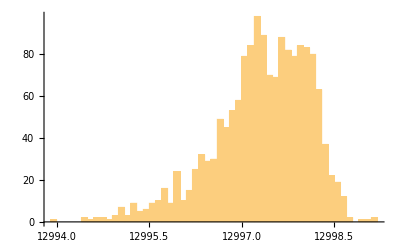

```mathematica
Histogram[zvals//Flatten,50]
```

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

Look at structure of the file

```mathematica
Manipulate[
ListPlot[Take[xvals,{ilow,ilow+chunk}],Joined->True,Mesh->All,PlotRange->All],{ilow,1,Length[xvals]-chunk-1,250},{{chunk,500},10,Length[xvals]-1,1},SaveDefinitions->True]
```

```mathematica
Manipulate[
ListPlot[Take[yvals,{ilow,ilow+chunk}],Joined->True,Mesh->All,PlotRange->All],{ilow,1,Length[yvals]-chunk-1,1},{{chunk,500},10,Length[yvals]-ilow,1},SaveDefinitions->True]
```

### Execute each point removal section separately and reset worksurf each time. Start next iteration above.

```mathematica
Interrupt[]
```

#### XY Range clean up next. Do each section separately, resetting the main lists each time to the smaller ones.

trim after setting x and y ranges above

```mathematica
{xmin,xmax}={Min[Take[worksurf,All,{1}]],Max[Take[worksurf,All,{1}]]};
{ymin,ymax}={Min[Take[worksurf,All,{2}]],Max[Take[worksurf,All,{2}]]};
{zmin,zmax}={Min[Take[worksurf,All,{3}]],Max[Take[worksurf,All,{3}]]};
```

```mathematica
{{xmin,xmax},{ymin,ymax},{zmin,zmax}}
```

{{1.3499,40.3502},{1.3499,40.3678},{12993.9,12999.1}}

```mathematica
{{xmin,xmax},{ymin,ymax},{zmin,zmax}}=Input["Enter min,max values here",{{xmin,xmax},{ymin,ymax},{zmin,zmax}}]
```

{{1.3499,40.3502},{1.3499,40.3678},{12993.9,12999.1}}

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

```mathematica
{xrange,yrange,zrange}={{xmin,xmax},{ymin,ymax},{zmin,zmax}}
```

{{1.3499,40.3502},{1.3499,40.3678},{12993.9,12999.1}}

```mathematica
xvals=Take[worksurf,All,{1}]//Flatten;
yvals=Take[worksurf,All,{2}]//Flatten;
zvals=Take[worksurf,All,{3}]//Flatten;
```

```mathematica
deltax=xmax-xmin;deltay=ymax-ymin;deltaz=zmax-zmin;{deltax,deltay,deltaz}
```

{39.0003,39.0179,5.21}

```mathematica
{xunit$,yunit$,zunit$}
```

{mm,mm,µm}

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

Skip to other clean-up section based on statistics, if desired. Restrict here by x and y range numbers.
NEVER reset worksurf. This is the unaltered input data.

```mathematica
Length[worksurf]
```

1600

```mathematica
test =
Reap[
 Do[
pt=worksurf[[i]];If[pt[[3]]<zrange[[2]]&& pt[[3]]>zrange[[1]]&&pt[[2]]<yrange[[2]]&& pt[[2]]>yrange[[1]]&&pt[[1]]<xrange[[2]]&& pt[[1]]>xrange[[1]]
,Sow[pt]]
,{i,Length[worksurf]}]
];
```

```mathematica
Short[test]
```

{Null,{{{2.34995,1.35251,12996.4},{«1»},«1589»,{«1»},{«1»}}}}

```mathematica
trimsurf=Drop[test,1]//Flatten[#,2]&;
```

```mathematica
Length[trimsurf]
```

1593

```mathematica
Remove[test]
```

```mathematica
(*worksurf=Delete[worksurf,plist];*)
```

```mathematica
xvals=Take[trimsurf,All,{1}]//Flatten;
yvals=Take[trimsurf,All,{2}]//Flatten;
zvals=Take[trimsurf,All,{3}]//Flatten;
```

```mathematica
fileinS
```

VIEW_sn19197

```mathematica
(*Interrupt[]*) (* to override default file name and ID by corner region of original input plot. *)
```

```mathematica
(*fileinS="110-03to06_"<>corner$*)
```

Subtract mean from z. Skip if integer.

```mathematica
meanzflag=False;
```

```mathematica
meanzflag=Input["Set meanzflag to subtract mean from trimsurf data",meanzflag]
```

False

```mathematica
If[meanzflag,meanz=Mean[zvals]//N;trimsurf=Map[MapAt[Plus[#,-meanz]&,#,3]&,trimsurf]]
```

```mathematica
trimsurf[[1;;10]]
```

{{2.34995,1.35251,12996.4},{3.34991,1.35505,12995.8},{4.34997,1.35759,12996.2},{5.34993,1.36014,12996.1},{6.34989,1.36268,12996.5},{7.34995,1.36522,12996.3},{8.3499,1.36776,12995.9},{10.35,1.35254,12996.4},{11.35,1.35509,12996.2},{12.35,1.35763,12996.9}}

```mathematica
xvals=Take[trimsurf,All,{1}]//Flatten;
yvals=Take[trimsurf,All,{2}]//Flatten;
zvals=Take[trimsurf,All,{3}]//Flatten;
```

```mathematica
{Mean[xvals],Mean[yvals],Mean[zvals]}//N
```

{20.8854,20.8487,12997.3}

```mathematica
{xmin=Min[xvals],Mean[xvals],xmax=Max[xvals]}//N
{ymin=Min[yvals],Mean[yvals],ymax=Max[yvals]}//N
{zmin=Min[zvals],Mean[zvals],zmax=Max[zvals]}//N
```

{1.34991,20.8854,40.3501}

{1.34991,20.8487,40.3677}

{12994.4,12997.3,12999.1}

```mathematica
{deltax=xmax-xmin, deltay=ymax-ymin,deltaz=zmax-zmin}
```

{39.0002,39.0178,4.67}

```mathematica
Length[trimsurf]
```

1593

#### Plot after trimming the X or Y range above. TRIM IT IN PLACE.

```mathematica
skipnum=0
```

0

```mathematica
lpp02=ListPointPlot3D[trimsurf,PlotRange->All,ViewPoint->{0,0,Infinity},ColorFunction->"Rainbow",AxesLabel->{"X "<>xunit$,"Y "<>yunit$,"Z "<>zunit$},PlotLabel->fileinS<>"\nSkip factor = "<>ToString[skipnum]<>", {rows,cols}="<>rowscols$]
```

-Graphics3D-

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

```mathematica
trimsurfplt=ListPointPlot3D[trimsurf,PlotRange->All,ColorFunction->"Rainbow",AxesLabel->{"X "<>xunit$,"Y "<>yunit$,"Z "<>zunit$},PlotLabel->fileinS<>"\nSkip factor = "<>ToString[skipnum]<>", {rows,cols}="<>rowscols$]
```

-Graphics3D-

```mathematica
(*ListDensityPlot[Take[worksurf,{1,-1,skipnum}],ColorFunction->"Rainbow",MaxPlotPoints->200,AspectRatio->Automatic]*)(*,Frame->True,FrameLabel->{"X[mm]","Y[mm]"}]]*)
```

### End of range clean-up iteration section. Contine after subregion is selected.

```mathematica
npts=Length[zvals]
```

1593

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

```mathematica
histplt=Histogram[zvals,50,ImageSize->400];
```

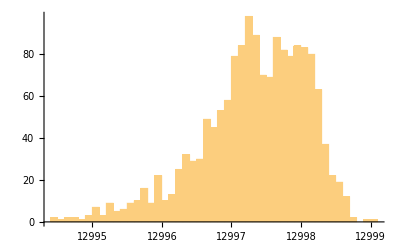

```mathematica
{histplt,Dynamic[MousePosition["Graphics"]]}
```

```mathematica
zsd=StandardDeviation[zvals]//N
```

0.761341

#### Select the appropriate Z trim criteria next. Leave lists empty to use all points without discarding any.

```mathematica
zminlist={};zmaxlist={};
```

```mathematica
{zmin,zmax}
```

{12994.4,12999.1}

```mathematica
{minq,maxq}=Input["Enter trim range according to histogram above",{zmin,zmax}]
```

{12994.4,12999.1}

Execute  the following  cell to set the z-trim region . Default is accept all points.

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

```mathematica
zmaxlist=Select[zvals,#> maxq &];
zminlist=Select[zvals,#< minq &];
```

#### Continue here after selecting points to discard, or if no points to discard. Skip if nothing to trim.

```mathematica
{Length[zmaxlist],Length[zminlist]}
```

{0,0}

```mathematica
Union[zmaxlist];
```

```mathematica
Length[%]
```

0

```mathematica
(* Share[] *)
```

```mathematica
outliers=Join[zminlist,zmaxlist];
```

```mathematica
Length[outliers]
```

0

```mathematica
outliers2=Union[outliers];
```

```mathematica
Short[outliers2]
```

{}

```mathematica
plist=Table[Position[zvals,outliers2[[i]]],{i,Length[outliers2]}];
Short[plist]
```

{}

```mathematica
plist=Flatten[plist,1];
```

```mathematica
meanXYZd=.
```

```mathematica
meanXYZt=.
```

```mathematica
trimsurf=Delete[trimsurf,plist];
```

Discard points from the list that lie outside the desired range. Note that the result is a list, not an array. Can't use plot functions that require an array for input.

top is a reduced-size array to use in fitting the surface to avoid excessive calculation time. reduce=1 uses all the points.

```mathematica
Length[worksurf]
```

1600

```mathematica
Length[trimsurf]
```

1593

```mathematica
trimsurfplt=ListPlot3D[trimsurf,PlotLabel->fileinS<>"\n{rows,cols}="<>rowscols$,PlotRange->All,BoxRatios->{1,1,.5},AxesLabel->{"X["<>xunit$<>"]","Y["<>yunit$<>"]","Z["<>zunit$<>"]"},ColorFunction->"Rainbow",ImageSize->500]
```

-Graphics3D-

```mathematica
top=.
```

Shorten the data array only if there are too many points. Need to change skipnum value first

```mathematica
skipnum2=.(* *(Length[worksurf]//Log[100,#]&//N//Floor) *)
```

```mathematica
zsdev=StandardDeviation[trimsurf][[3]]//N
```

0.761341

```mathematica
rowscols$="sparse";ToString[{nRows,nCols}]
```

{nRows, nCols}

```mathematica
topplt=ListPlot3D[trimsurf,PlotLabel->fileinS<>"\n{rows,cols}="<>rowscols$,PlotRange->All,BoxRatios->{1,1,.5},AxesLabel->{"X["<>xunit$<>"]","Y["<>yunit$<>"]","Z["<>zunit$<>"]"},ColorFunction->"Rainbow",ImageSize->500]
```

-Graphics3D-

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

Set the worksurf to the above trimsurf. Go back up to trim more if desired.

```mathematica
worksurf=trimsurf;
```

```mathematica
NotebookLocate["Start trim"]
```

### Fit edited list to a surface. Enter the surface fit order next. A general set of basis polynomials is calculated and the fit is performed. Enter the x and y orders separately

#### COntinue after fit selection

Select one of the button options, then continue

```mathematica
fitflag=.;fitidxS$=.;fitord$=.
```

```mathematica
fitnumflag=Input["Enter num for fit to apply.\n-1=no detrending\n0 = piston only\n1 = pure plane\n2 = pure sphere\n3 = general {m,n}order polynomial\n4 = Chebyshev polynomial (m,n)" ]
```

1

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

The working array is worksurf. Make sure it has the desired data in it.

Need to normalize the x and y values when doing the Chebyshev fit, using the actual values for xlen and ylen. For the other cases, use xlen=ylen=1 in the normaization expression.

```mathematica
xlen=1;ylen=1;
```

```mathematica
Switch[fitnumflag,
-1,(*No detrend*)fitidxS$="none";Print["No detrend"];fitbasis={0},

0,(*Piston only*)fitbasis={1};fitidxS$="0";Print["Piston only fit"],
1, (*Pure Plane*)fitbasis={1,x,y};fitidxS$="1,1"(*fitord$=StringTake[ToString[fitbasis],{2,-2}]*),
2,(*Pure Sphere*)fitbasis={1,x,y,x y,x^2+y^2};fitidxS$="2,2"(*fitord$=StringTake[ToString[fitbasis//InputForm],{2,-2}]*),

3,(*General cartesian polynomial*)fitidxS$=InputString["Enter x and y order numbers of 2D surface fit desired, separated by a comma, i.e. 1,2"];
sp=StringSplit[fitidxS$,","]//ToExpression;
ordx=sp[[1]];ordy=sp[[2]];
(*fitord$=StringTake[ToString[sp],{2,-2}];*)
fitbasis={};
Do[
If[i+j>ordx+ordy,Null,AppendTo[fitbasis,x^i y^j]],{i,0,ordx},{j,ordy,0,-1}],

4,(*Chebychev poly*)fitidxS$=InputString["Enter x and y order numbers of 2D surface fit desired, separated by a comma, i.e. 1,2"];
sp=StringSplit[fitidxS$,","]//ToExpression;
ordx=sp[[1]];ordy=sp[[2]];
fitidxS$=fitidxS$<>"Chb";
(*fitord$=StringTake[ToString[sp],{2,-2}];*)
(*compute the required xlen and ylen for this case*)
xlen=xmax-xmin//N;ylen=ymax-ymin//N;
fitbasis={};
xs[x_,xmax_,xmin_]:=2/(xmax-xmin) (x-xmin-(xmax-xmin)/2);
fitbasis=Table[HoldForm[ChebyshevT[ii,xs[x,xmax,xmin]]] HoldForm[ChebyshevT[jj,xs[y,ymax,ymin]]]/.ii->i/.jj->j,{i,0,ordx},{j,0,ordy}]//Flatten;

]
```

1,1

```mathematica
fitbasis//ReleaseHold//ColumnForm;
```

```mathematica
fitidxS$
```

1,1

```mathematica
Interrupt[]
```

For Chebyshev, need to release the hold, then Sort the fitbasis to get it in the same order as comes out of the Fit result.
Need to sort the expanded funtions in terms of the highest powers of x and y. Sorting on y lets x-index run fast. This seems to work on both lists.

```mathematica
(*fitbasis2=fitbasis//ReleaseHold;
fitbasissort=fitbasis2//Sort[#,((Exponent[#1,y]<=Exponent[#2,y])&&True)&]&;
fitbasissort//ColumnForm  *)
```

Now calc and sort the fit expression. Need to convert the Head Plus to List by Apply.

```mathematica
surffit=Fit[worksurf,fitbasis//ReleaseHold,{x,y}];
```

```mathematica
surffit
```

12998.3-0.0291561 x-0.017136 y

```mathematica
Apply[List,surffit,Heads->True]//ColumnForm;
```

Add separate case here for Chebyshev. Normalize the x and y values before fittiing.

```mathematica
temp=worksurf;
```

```mathematica
temp=Map[MapAt[Divide[#,xlen]&,#,1]&,temp];
temp=Map[MapAt[Divide[#,ylen]&,#,2]&,temp];
```

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

```mathematica
fitsurfplt=Plot3D[surffit,{x,xmin,xmax},{y,ymin,ymax},ColorFunction->"Rainbow",ImageSize->400,PlotLabel->fileinS<>"\nSfit:"<>fitidxS$<>", Rfit:"<>fitidxR$]
```

-Graphics3D-

```mathematica
Button["Export fit surface plot file",Export[foutname2<>"_fitsurf.tiff",fitsurfplt,"ImageEncoding"->"LZW",ImageResolution->100,Method->"Queued"]]
```

Export fit surface plot file

```mathematica
If[testdataflag,testdataflag=False;Interrupt[],Null]
```

If[testdataflag,testdataflag=False;Interrupt[],Null]

When rawXYZ values are in meter units, the radius is in units of meters.

```mathematica
If[c0x!=0.0,Rx=1/(2*c0x),Rx=Infinity]
```

If[c0x≠0.,Rx=1/(2 c0x),Rx=∞]

```mathematica
fileinS
```

VIEW_sn19197

```mathematica
StringForm["Radius from full 3D surface fit is `` m.",NumberForm[Rx,5]]
```

Radius from full 3D surface fit is Rx m.

Subtract the selected fit from the data. Default is plane fit subtraction.

```mathematica
meanXYZdetrend=.
```

```mathematica
meanXYZtd=.
```

```mathematica
(*cloudXYZtrdet=Table[{cloudXYZ[[i,1]],cloudXYZ[[i,2]],cloudXYZ[[i,3]]-surffit[cloudXYZ[[i,1]],cloudXYZ[[i,2]]]}
,{i,1,Length[cloudXYZ]}
];*)
```

```mathematica
(*cloudXYZtrdet=Table[{sparsetop[[i,1]],sparsetop[[i,2]],sparsetop[[i,3]]-surffit/.x->sparsetop[[i,1]]/.y->sparsetop[[i,2]]}
,{i,1,Length[sparsetop]}
];*)
```

```mathematica
resids=.
```

```mathematica
detrworksurf=Table[{worksurf[[i,1]],worksurf[[i,2]],worksurf[[i,3]]-surffit/.x->worksurf[[i,1]]/.y->worksurf[[i,2]]}
,{i,1,Length[worksurf]}
];
```

```mathematica
zresids=.
```

```mathematica
zcloudresids=Take[detrworksurf,All,{3}]//Flatten;
```

```mathematica
maxz=Max[zcloudresids];minz=Min[zcloudresids];sigma=StandardDeviation[zcloudresids];
```

```mathematica
sig$=ToString[sigma//NumberForm[#,3]&]
```

0.654

```mathematica
{maxz,minz,sigma}
```

{1.46551,-2.47301,0.654061}

```mathematica
Short[zcloudresids]
```

{-1.74381,-2.36461,«1590»,-0.397576}

```mathematica
zbin=BinCounts[zcloudresids,(maxz-minz)/50]
```

{2,2,4,5,3,3,4,7,6,14,9,8,10,7,9,4,13,18,15,16,15,8,24,27,27,28,31,40,54,52,71,72,94,93,126,107,111,112,83,71,77,44,25,18,11,6,4,2,0,0,1}

```mathematica
hrange[binlist_,min_,max_]:=Quantile[binlist,{min,max}]
```

```mathematica
hgtrange=.
```

```mathematica
PV99rangelist=hrange[zcloudresids,0.005,0.995];
PV99range$=ToString[PV99rangelist//NumberForm[#,{6,2}]&]
PV95rangelist=hrange[zcloudresids,0.025,0.975];
PV95range$=ToString[PV99rangelist//NumberForm[#,{6,2}]&]
```

{-2.31, 1.07}

{-2.31, 1.07}

```mathematica
{PV99val=PV99rangelist[[2]]-PV99rangelist[[1]],PV95val=PV95rangelist[[2]]-PV95rangelist[[1]]}
```

{3.3799,2.65281}

```mathematica
{PV99$=ToString[PV99val//NumberForm[#,{4,2}]&],
PV95$=ToString[PV95val//NumberForm[#,{4,2}]&]}
```

{3.38,2.65}

```mathematica
fitidxR$
```

0,0

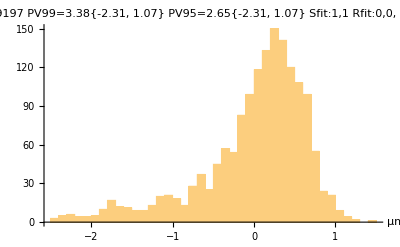

```mathematica
histresidplt=Histogram[zcloudresids,50,ImageSize->400,AxesLabel->{zunit$,""},PlotLabel->fileinS<>"\nPV99="<>PV99$<>PV99range$<>"\nPV95="<>PV95$<>PV95range$<>"\nSfit:"<>fitidxS$<>" Rfit:"<>fitidxR$<>", sdev="<>sig$<>zunit$]
```

```mathematica
Button["Export histresid plot file",Export[foutname2<>"_"<>sig$<>"_histSR.tiff",histresidplt,"ImageEncoding"->"LZW",ImageResolution->100]]
```

Export histresid plot file

```mathematica
accumulatedCount[bins_,counts_]:=Accumulate[counts]
```

```mathematica
hrange[zcloudresids,0.025,0.975]
```

{-1.7786,0.874219}

```mathematica
hrange[zcloudresids,0.005,0.995]
```

{-2.30587,1.07403}

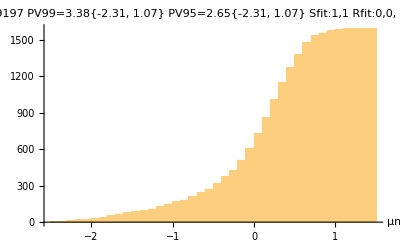

```mathematica
histcumplt=Histogram[zcloudresids,50,accumulatedCount,PlotLabel->fileinS<>"\nPV99="<>PV99$<>PV99range$<>"\nPV95="<>PV95$<>PV95range$<>"\nSfit:"<>fitidxS$<>" Rfit:"<>fitidxR$<>", sdev="<>sig$<>zunit$,AxesLabel->{zunit$,""}]
```

```mathematica
Button["Export histcum plot file",Export[foutname2<>"_"<>sig$<>"_histcumSR.tiff",histcumplt,"ImageEncoding"->"LZW",ImageResolution->100]]
```

Export histcum plot file

```mathematica
quantlist={0.0,0.005,0.01,0.025,0.50,.975,0.99,0.995,1.0};
```

```mathematica
qres=Quantile[zcloudresids,quantlist]
```

{-2.47301,-2.30587,-2.15615,-1.7786,0.158772,0.874219,1.00383,1.07403,1.46551}

```mathematica
qtable=Transpose[{quantlist,qres}];%//TableForm
```

-2.47301
-2.30587
-2.15615
-1.7786
0.158772
0.874219
1.00383
1.07403
1.46551

```mathematica
q99range=qres[[8]]-qres[[2]]
```

3.3799

```mathematica
q95val$=qres[[7]]-qres[[3]]//ToString
```

3.15998

```mathematica
q95range$={qres[[3]],qres[[8]]}//ToString
```

{-2.15615, 1.07403}

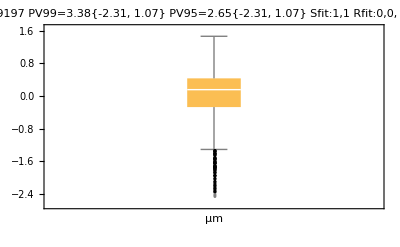

```mathematica
bwc=BoxWhiskerChart[zcloudresids,"Outliers",ImageSize->400,PlotLabel->fileinS<>"\nPV99="<>PV99$<>PV99range$<>"\nPV95="<>PV95$<>PV95range$<>"\nSfit:"<>fitidxS$<>" Rfit:"<>fitidxR$<>", sdev="<>sig$<>zunit$,AxesLabel->{zunit$,""}]
```

```mathematica
Button["Export box whisker chart file",Export[foutname2<>"_"<>sig$<>"_boxwhisker.tiff",bwc,"ImageEncoding"->"LZW",ImageResolution->100]]
```

Export box whisker chart file

```mathematica
ChartElementData["BoxWhiskerChart"]
```

{BoxWhisker,FadingBoxWhisker,GlassBoxWhisker,GradientScaleBoxWhisker,PlateauBoxWhisker}

```mathematica
filein
```

filein

Write out the quantile info to xls file and all zresids to text file.

```mathematica
Export[fileinS<>"-"<>sig$<>"_"<>fitidxS$<>"_zresids.txt",zcloudresids,"Text"]
```

VIEW_sn19197-0.654_1,1_zresids.txt

```mathematica
Export[fileinS<>"-"<>sig$<>"_"<>fitidxS$<>"_Quantiles.xls",Prepend[qtable,{fileinS<>"\nPV99="<>PV99$<>PV99range$<>",PV95="<>q95val$<>q95range$<>"\nSfit:"<>fitidxS$<>" Rfit:"<>fitidxR$<>", sdev="<>sig$<>zunit$}]//TableForm,"XLS"]
```

VIEW_sn19197-0.654_1,1_Quantiles.xls

```mathematica
binwid=(maxz-minz)/25;
```

```mathematica
bcts=BinCounts[zcloudresids,binwid]
```

{4,9,6,11,20,17,17,13,31,31,23,51,55,71,106,143,187,233,223,154,121,43,17,6,0,1}

```mathematica
Mean[zcloudresids]
```

-1.60737×10^-13

```mathematica
sd=sigma//N
```

0.654061

```mathematica
(*sd=StandardDeviation[zcloudresids]//N *)
```

```mathematica
MeanDeviation[zcloudresids]//N
```

0.488032

```mathematica
MedianDeviation[zcloudresids]
```

0.324315

```mathematica
zwid=4 sd
```

2.61624

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

#### Plot detrended trim array. Eliminate the dropouts with the RegionFunction.

```mathematica
Function[{x,y,z},Hue[z]]
```

Function[{x,y,z},Hue[z]]

```mathematica
Length[detrworksurf]
```

1593

```mathematica
Max[zvals]
```

12999.1

```mathematica
{minz,maxz}={Min[zcloudresids],Max[zcloudresids]}
```

{-2.47301,1.46551}

```mathematica
PV=maxz-minz
```

3.93852

```mathematica
zrange={minz,maxz}
```

{-2.47301,1.46551}

Plot detrended point cloud next:

```mathematica
skipnum
```

0

```mathematica
vp=.
```

```mathematica
vp=Options[ListPointPlot3D,ViewPoint][[1,2]]
```

{1.3,-2.4,2.}

```mathematica
Dynamic[vp]
```

```mathematica
lpplt=ListPointPlot3D[detrworksurf,PlotRange->All,ColorFunction->"Rainbow",(*BoxRatios->{Automatic,Automatic,Automatic},*)AxesLabel->{"Xval","Yval","Z["<>zunit$<>"]"},PlotLabel->fileinS<>"\nPV99="<>PV99$<>PV99range$<>"\nPV95="<>PV95$<>PV95range$<>"\nSfit:"<>fitidxS$<>" Rfit:"<>fitidxR$<>", sdev="<>sig$<>zunit$,ImageSize->400,ViewPoint->Dynamic[vp],PlotLegends->Automatic]
```

-Graphics3D-

```mathematica
Dynamic[vp]
```

```mathematica
sig$
```

0.654

```mathematica
foutname2=fileinS<>"-"<>"S"<>fitidxS$<>"_R"<>fitidxR$
```

VIEW_sn19197-S1,1_R0,0

Output the detrended data triplets

```mathematica
Button["Export detrworksurf data text file",Export[foutname2<>"_DetrendXYZ.txt",detrworksurf,"Text"],Method->"Queued"]
```

Export detrworksurf data text file

```mathematica
lpplt2=Show[lpplt,ViewPoint->Dynamic[vp]]
```

-Graphics3D-

```mathematica
Button["Export lpplt2 plot file",Export[foutname2<>"_"<>sig$<>"_cloud.tiff",lpplt2,"ImageEncoding"->"LZW",ImageResolution->100,Method->"Queued"]]
```

Export lpplt2 plot file

```mathematica
Directory[]
```

/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/_ITL pending/Pre First Art mech sample data/VIEW_sn19197_files

Define a tick function to scale the values by some scaleval factor

```mathematica
ticksw[wmin_,wmax_,scaleval_,interval_]:=Table[{i,Floor[i  scaleval]},{i,wmin,wmax,interval}]
```

```mathematica
{xmin,xmax,ymin,ymax}
```

{1.34991,40.3501,1.34991,40.3677}

```mathematica
lpdetr=ListPlot3D[detrworksurf,InterpolationOrder->2,ImageSize->400,PlotRange->{minz,maxz},BoxRatios->{deltax/deltay,1,1/2},Mesh->None,ColorFunction->"Rainbow",ColorFunctionScaling->True,AxesLabel->{"Xcol["<>xunit$<>"]","Yrow["<>yunit$<>"]","Z["<>zunit$<>"]"},PlotLabel->fileinS<>"\nPV99="<>PV99$<>PV99range$<>"\nPV95="<>PV95$<>PV95range$<>"\nSfit:"<>fitidxS$<>" Rfit:"<>fitidxR$<>", sdev="<>sig$<>zunit$,Ticks->{ticksw[xmin,xmax,1,Ceiling[(xmax-xmin)/6,10]],ticksw[ymin,ymax,1,Ceiling[(ymax-ymin)/6,10]],Automatic},PlotLegends->Automatic]
```

-Graphics3D-

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

```mathematica
lpdetr2=lpdetr
```

-Graphics3D-

```mathematica
Button["Export lpdetr2 plot file",Export[foutname2<>"_"<>sig$<>"_fitSR.tiff",lpdetr2,"ImageEncoding"->"LZW",ImageResolution->100],Method->"Queued"]
```

Export lpdetr2 plot file

Compute list resids. These are xyz triplets.

```mathematica
(*Share[]*)
```

```mathematica
zsd=StandardDeviation[detrworksurf][[3]]
```

0.654061

```mathematica
zsd==sigma
```

True

```mathematica
lpresid=.;lpresid2=.;
```

```mathematica
plotallflag=True;
```

```mathematica
skipnum
```

0

```mathematica
If[plotallflag,lpresid=ListPlot3D[detrworksurf,PlotRange->{All,All,{minz,maxz}},ColorFunction->"Rainbow",BoxRatios->{deltax/deltay,1,1/2},ColorFunctionScaling->True,AxesLabel->{"Xcol["<>xunit$<>"]","Yrow["<>yunit$<>"]","Z["<>zunit$<>"]"},PlotLabel->fileinS<>"\nPV99="<>PV99$<>PV99range$<>"\nPV95="<>PV95$<>PV95range$<>"\nSfit:"<>fitidxS$<>" Rfit:"<>fitidxR$<>", sdev="<>sig$<>zunit$,ImageSize->400,Ticks->{ticksw[xmin,xmax,1,Ceiling[(xmax-xmin)/6,10]],ticksw[ymin,ymax,1,Ceiling[(ymax-ymin)/6,10]],Automatic},PlotLegends->Automatic]; 
lpresid2=lpresid
]
```

-Graphics3D-

```mathematica
foutname2<>ToString[sig$]
```

VIEW_sn19197-S1,1_R0,00.654

```mathematica
Button["Export lpresid2 plot file",Export[foutname2<>"_"<>sig$<>"_fitSR2.tiff",lpresid2,"ImageEncoding"->"LZW",ImageResolution->100],Method->"Queued"]
```

Export lpresid2 plot file

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

```mathematica
ColorData["Named"]
```

{Atoms,Crayola,GeologicAges,HTML,Legacy,WebSafe}

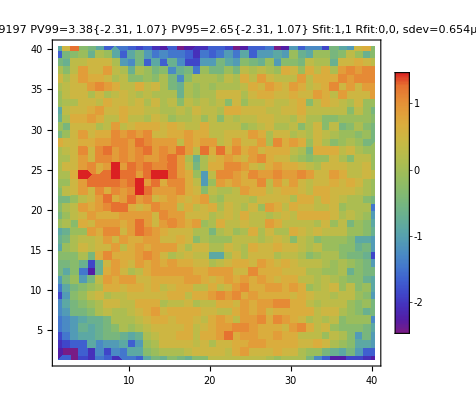

```mathematica
cplt=ListContourPlot[detrworksurf,ColorFunction->"Rainbow",Contours->20,PlotLabel->fileinS<>"\nPV99="<>PV99$<>PV99range$<>"\nPV95="<>PV95$<>PV95range$<>"\nSfit:"<>fitidxS$<>" Rfit:"<>fitidxR$<>", sdev="<>sig$<>zunit$,PlotLegends->Automatic,InterpolationOrder->0]
```

```mathematica
Button["Export contour plot file",Export[foutname2<>"_"<>sig$<>"_contour.tiff",cplt,"ImageEncoding"->"LZW",ImageResolution->100],Method->"Queued"]
```

Export contour plot file

Iterate selection next:

```mathematica
Input["Select one of the worksurf assignments.\nOr just go back up to new fit to use previous data."]
```

```mathematica
worksurf=detrworksurf; (* if you like the current detrened surface *)
```

```mathematica
worksurf=trimsurf; (* if you want to restart with the original trimmed data *)
```

To iterate, execute one of the next locates.

```mathematica
NotebookLocate["new fit" ] (* go back up to change the fit order with the original data *)
```

```mathematica
NotebookLocate["Remove bad points"] (* to remove more bad points from worksurf *)
```

```mathematica
NotebookLocate["Restart from urdataSR"] (* to restore all the trimmed points and restart the analysis *)
```

Define array names:
  ursurf == Initial input data readin
  trimsurf == trimmed of bad points
  worksurf == working array starting point for detrending
  detrworksurf == work surf after detrending

For next input file:

```mathematica
NotebookLocate["pick MST file num"]
```

### Countor plots next

resids are triplets

```mathematica
Dimensions[detrworksurf]
```

{1593,3}

```mathematica
cloudXYZtrdet=detrworksurf;
```

```mathematica
Dimensions[cloudXYZtrdet]
```

{1593,3}

```mathematica
cloudXYZtrdet[[1;;10]]
```

{{2.34995,1.35251,12996.4},{3.34991,1.35505,12995.8},{4.34997,1.35759,12996.2},{5.34993,1.36014,12996.1},{6.34989,1.36268,12996.5},{7.34995,1.36522,12996.3},{8.3499,1.36776,12995.9},{10.35,1.35254,12996.4},{11.35,1.35509,12996.2},{12.35,1.35763,12996.9}}

```mathematica
Zstddev=StandardDeviation[cloudXYZtrdet][[3]]
```

0.761341

```mathematica
{minX,maxX}={Min[Take[cloudXYZtrdet,All,{1}]],Max[Take[cloudXYZtrdet,All,{1}]]};
{minY,maxY}={Min[Take[cloudXYZtrdet,All,{2}]],Max[Take[cloudXYZtrdet,All,{2}]]};
{minz1,maxz1}={Min[Take[cloudXYZtrdet,All,{3}]],Max[Take[cloudXYZtrdet,All,{3}]]}
```

{12994.4,12999.1}

```mathematica
(*{minz1,maxz1}={-6,6}*Zstddev *)
```

```mathematica
PlotLabel->fileinS<>"\nPV99="<>PV99$<>PV99range$<>"\nPV95="<>PV95$<>PV95range$<>"\nSfit:"<>fitidxS$<>" Rfit:"<>fitidxR$<>", sdev="<>sig$<>zunit$
```

PlotLabel→VIEW_sn19197
PV99=3.84{12994.80, 12998.70}
PV95=3.00{12994.80, 12998.70}
Sfit:none Rfit:0,0, sdev=0.761µm

```mathematica
fileinS
```

VIEW_sn19197

```mathematica
PlotLabel->fileinS<>"\nPV99="<>PV99$<>PV99range$<>"\nPV95="<>PV95$<>PV95range$<>"\nSfit:"<>fitidxS$<>" Rfit:"<>fitidxR$<>", sdev="<>sig$<>zunit$
```

PlotLabel→VIEW_sn19197
PV99=3.84{12994.80, 12998.70}
PV95=3.00{12994.80, 12998.70}
Sfit:none Rfit:0,0, sdev=0.761µm

```mathematica
PlotRange->{{0,(maxz1-minz1)/21},{minz1,maxz1}}
```

PlotRange→{{0,0.222381},{12994.4,12999.1}}

```mathematica
AxesLabel->{"X["<>xunit$<>"]","Y["<>yunit$<>"]"}
```

AxesLabel→{X[mm],Y[mm]}

```mathematica
{minz1,maxz1}
```

{12994.4,12999.1}

```mathematica
PV=maxz1-minz1
```

4.67

```mathematica
aspct=(xrange[[2]]-xrange[[1]])/(yrange[[2]]-yrange[[1]])
```

0.999547

```mathematica
FrameTicks->{ticksw[xmin,xmax,delx,150],ticksw[ymin,ymax,dely,150]}
```

FrameTicks→{{{1.34991,Floor[1.34991 delx]}},{{1.34991,Floor[1.34991 dely]}}}

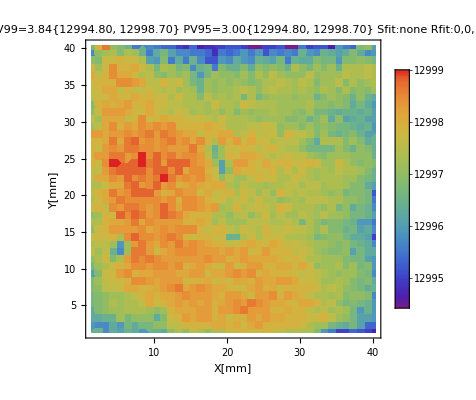

```mathematica
cplt=ListContourPlot[cloudXYZtrdet,PlotRange->All,Contours->25,InterpolationOrder->0,Axes->False,FrameLabel->{"X["<>xunit$<>"]","Y["<>yunit$<>"]"},ColorFunction->"Rainbow",Mesh->False,ImageSize->400 ,AspectRatio->Automatic,PlotLabel->fileinS<>"\nPV99="<>PV99$<>PV99range$<>"\nPV95="<>PV95$<>PV95range$<>"\nSfit:"<>fitidxS$<>" Rfit:"<>fitidxR$<>", sdev="<>sig$<>zunit$,PlotLegends->Automatic]
```

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

```mathematica
Button["Export cplt contour plot file",Export[foutname2<>"_"<>sig$<>"_contour2.tiff",cplt,"ImageEncoding"->"LZW",ImageResolution->100]]
```

Export cplt contour plot file

```mathematica
Button["Export cplt contour plot PNG file",Export[foutname2<>"_"<>sig$<>"_contour2.png",cplt,"ImageEncoding"->"LZW",ImageResolution->100,Method->"Queued"]]
```

Export cplt contour plot PNG file

```mathematica
Dimensions[cloudXYZtrdet]
```

{1593,3}

```mathematica
Short[cloudXYZtrdet,5]
```

{{2.34995,1.35251,-0.869303},{3.34991,1.35505,-1.5193},{4.34997,1.35759,-1.0793},{5.34993,1.36014,-1.2593},«1585»,{37.35,40.3629,-1.9493},{38.35,40.3654,-0.639303},{39.3499,40.3501,-0.409303},{40.3499,40.3526,-1.2993}}

```mathematica
NotebookLocate["iteration start"]
```

```mathematica
NotebookLocate["pick MST file num"]
```

## View sections of the original big surface in datain3. Compute surface gradient plot on selected area. (Not for FREEFORM data)

```mathematica
Dimensions[sparseXYZtrdet]
```

```mathematica
(*datain3=resids; *)
```

```mathematica
datain3[[1]]
```

```mathematica
nrows
```

```mathematica
ncols
```

```mathematica
ncols nrows
```

```mathematica
Length[datain3]
```

```mathematica
Length[datain3]/ncols
```

```mathematica
datain32D=.
```

Partition the original datain3 triplets into a 2D array.

```mathematica
datain3[[1]]
```

```mathematica
datain32D=Partition[datain3,ncols];
```

```mathematica
Length[datain32D]
```

```mathematica
fitidxS$=InputString["Enter x and y order numbers of 2D surface fit desired, separated by a comma, i.e. 1,2"];
sp=StringSplit[fitidxS$,","]//ToExpression;
ordx=sp[[1]];ordy=sp[[2]];
fitbasis={};
Do[
If[i+j>ordx+ordy,Null,AppendTo[fitbasis,x^i y^j]],{i,0,ordx},{j,0,ordy-i}];fitbasis
```

```mathematica
Dimensions[datain32D]
```

```mathematica
rstart=1;rinc=10;colleft=1;colinc=20;
```

```mathematica
Manipulate[
subdatlist=Take[datain32D,{rstart,rstart+rinc},{colleft,colleft+colinc}]//Flatten[#,1]&;
surffit[x_,y_]=Fit[subdatlist,fitbasis,{x,y}];

resids=Table[{subdatlist[[i,1]],subdatlist[[i,2]],subdatlist[[i,3]]-surffit[subdatlist[[i,1]],subdatlist[[i,2]]]}
,{i,1,Length[subdatlist]}
];
residsZ=Take[resids,All,{3}]//Flatten;
sdz=StandardDeviation[residsZ];
residsZarr=Partition[residsZ,colinc+1];
range$=ToString[{{rstart,rstart+rinc},{colleft,colleft+colinc}}];
ListPlot3D[residsZarr,ColorFunction->Automatic,Mesh->False,PlotRange->All,MaxPlotPoints->200,BoxRatios->{(colinc/rinc),1,1/2},PlotLabel->filein<>"\nStdDev="<>ToString[sdz]<>", Pixel size="<>ToString[pixSize]<>", Range="<>range$,DataRange->{delx{colleft,colleft+colinc},dely{rstart,rstart+rinc}},AxesLabel->{"Col X[µm]","Row Y[µm]","Z[µm]"}],

{{rstart,1,"Start row"},1,nrows-rinc-1,1,Appearance->"Open"},{{rinc,20,"Row range"},1,nrows-rstart-1,1,Appearance->"Open"},{{colleft,1,"LeftColmn"},1,ncols-colinc-1,1,Appearance->"Open"},{{colinc,Ceiling[(ncols-colleft)/10],"DeltaColmns"},1,ncols-colleft,1,Appearance->"Open"},
TrackedSymbols:>True,ContinuousAction->False,SynchronousUpdating->False,AppearanceElements->All,LocalizeVariables->False,SaveDefinitions->True]
```

```mathematica
datain32D//Short[#,10]&
```

```mathematica
Histogram[residsZ,AxesLabel->{zunit$,""},PlotLabel->filein<>"\nStdDev="<>ToString[sdz]<>", RCrange="<>range$]
```

```mathematica
residsZarr[[10,10]]
```

```mathematica
mediansd1=MedianDeviation[residsZ]
```

What is corrct normalization for slope kernal? 2pt differences should just divide by delx.

```mathematica
lanN=4;
```

```mathematica
lanczoslist=Table[3 k /(lanN (lanN+1) (2 lanN +1)),{k,-lanN,lanN}]
```

```mathematica
lancospos= Table[{lanN+1,i},{i,1,2 lanN +1}]
```

```mathematica
lkernal=SparseArray[lancospos->lanczoslist,2 lanN +1]
```

```mathematica
lanczosmatrixX[lanN_]:=Module[{},lanczoslist=Table[3 k /(lanN (lanN+1) (2 lanN +1)),{k,-lanN,lanN}];lancospos= Table[{lanN+1,i},{i,1,2 lanN +1}];
lkernal=SparseArray[lancospos->lanczoslist,2 lanN +1];
lk=lkernal//Normal
]
```

```mathematica
lanczosmatrixY[lanN_]:=Module[{},lanczoslist=Table[3 k /(lanN (lanN+1) (2 lanN +1)),{k,-lanN,lanN}];lancospos= Table[{lanN+1,i},{i,1,2 lanN +1}];
lkernal=SparseArray[lancospos->lanczoslist,2 lanN +1];
lk=Transpose[lkernal]//Normal
]
```

```mathematica
lanczosmatrixY[lanN]
```

```mathematica
lanczosmatrix[lanN_]:=Module[{},lanczoslist=Table[3 k /(lanN (lanN+1) (2 lanN +1)),{k,-lanN,lanN}];lancospos= Table[{lanN+1,i},{i,1,2 lanN +1}];
lkernal=SparseArray[lancospos->lanczoslist,2 lanN +1];
lk=lkernal+Transpose[lkernal]//Normal
]
```

```mathematica
delx
```

```mathematica
toMicroRad=10^6;
```

```mathematica
slopex=ListConvolve[lanczosmatrixX[lanN],residsZarr]toMicroRad/delx;
```

```mathematica
slopey=ListConvolve[lanczosmatrixY[lanN],residsZarr]toMicroRad/delx;
```

```mathematica
slopexy=ListConvolve[lanczosmatrix[lanN],residsZarr]toMicroRad/delx;
```

```mathematica
meanslp=Mean[StandardDeviation[slopexy]]*toMicroRad (* in microrads *)
```

```mathematica
medianslp=Median[StandardDeviation[slopexy]]*toMicroRad (* in microrads *)
```

```mathematica
gradient=Sqrt[slopex^2 +slopey^2];
```

```mathematica
medGrad=Median[StandardDeviation[gradient]]
```

```mathematica
Max[gradient]
```

```mathematica
Min[gradient]
```

```mathematica
sd2D
```

```mathematica
StandardDeviation[Flatten[gradient]]
```

```mathematica
meansdg=Mean[StandardDeviation[gradient]] (* in microrads *)
```

```mathematica
StandardDeviation[Flatten[gradient]]
```

```mathematica
(*gradient2=ListConvolve[{{1,1,1}/3,{1,1,1}/3},gradient];*)
```

```mathematica
gradientplt=ListPlot3D[gradient,ColorFunction->Automatic,Mesh->False,ImageSize->400,PlotRange->{0,10 medGrad},MaxPlotPoints->200,BoxRatios->{(colinc/rinc),1,1/2},DataRange->{delx{colleft,colleft+colinc},dely{rstart,rstart+rinc}},PlotLabel->filein<>"\n2D Gradient Mag StdDev="<>ToString[Mean[StandardDeviation[gradient]]]<>" µrad, Range="<>range$,AxesLabel->{"Col X[µm]","Row Y[µm]","Slope[µrad]"}]
```

```mathematica
ListContourPlot[gradient]
```

```mathematica
ListPlot3D[slopexy ,ColorFunction->Automatic,Mesh->False,PlotRange->All,ImageSize->400,MaxPlotPoints->200,BoxRatios->{(colinc/rinc),1,1/2},DataRange->{delx{colleft,colleft+colinc},dely{rstart,rstart+rinc}},PlotLabel->filein<>"\nSlope StdDev="<>ToString[Mean[StandardDeviation[slopexy]] ]<>" µrad, Range="<>range$,AxesLabel->{"Col X[µm]","Row Y[µm]","Slope[µrad]"}]
```

```mathematica
(* Share[] *)
```

```mathematica
Mean[StandardDeviation[slopexy]] (* in microrads *)
```

```mathematica
Dimensions[slopex]
```

```mathematica
Show[bumpslopeplt]
```

```mathematica
ListPlot3D[slopex ,ColorFunction->Automatic,Mesh->False,PlotRange->All,ImageSize->400,MaxPlotPoints->200,BoxRatios->{(colinc/rinc),1,1/2},DataRange->{delx{colleft,colleft+colinc},dely{rstart,rstart+rinc}},PlotLabel->filein<>"\nSlope StdDev="<>ToString[Mean[StandardDeviation[slopex]]]<>" µrad, Range="<>range$,AxesLabel->{"Col X[µm]","Row Y[µm]","Slope[µrad]"}]
```

```mathematica
ListPlot3D[slopey ,ColorFunction->Automatic,Mesh->False,PlotRange->All,ImageSize->400,MaxPlotPoints->200,BoxRatios->{(colinc/rinc),1,1/2},DataRange->{delx{colleft,colleft+colinc},dely{rstart,rstart+rinc}},PlotLabel->filein<>"\nSlope StdDev="<>ToString[Mean[StandardDeviation[slopey]]]<>" µrad, Range="<>range$,AxesLabel->{"Col X[µm]","Row Y[µm]","Slope[µrad]"}]
```

```mathematica
ListPlot3D[(slopex+slopey) ,ColorFunction->Automatic,Mesh->False,PlotRange->Automatic,MaxPlotPoints->200,BoxRatios->{(colinc/rinc),1,1/2},DataRange->{delx{colleft,colleft+colinc},dely{rstart,rstart+rinc}},ImageSize->400,PlotLabel->filein<>"\nSlope StdDev="<>ToString[Mean[StandardDeviation[slopex+slopey]]*10^6 ]<>" µrad, Range="<>range$,AxesLabel->{"Col X[µm]","Row Y[µm]","Slope[µrad]"}]
```

## Junk

#### Yvals: Remove points from list with yvals outside of desired range.

```mathematica
yrange={40,80};(*Clean up outliers from tile*)
```

```mathematica
yrange={64,66};
```

```mathematica
ymaxlist=Select[yvals,#>yrange[[2]] &];yminlist=Select[yvals,#<yrange[[1]] &];
```

```mathematica
Length[ymaxlist]
```

```mathematica
outliers=Join[yminlist,ymaxlist];
```

```mathematica
Length[outliers]
```

```mathematica
outliers2=Union[outliers];
```

```mathematica
ProgressIndicator[Dynamic[nn],{1,Length[outliers2]}]
```

```mathematica
plist=Table[(nn=i;Position[yvals,outliers2[[i]]]),{i,Length[outliers2]}];
Short[plist]
```

```mathematica
plist=Flatten[plist,1];
```

```mathematica
Interrupt[]
```

```mathematica
test=Reap[Map[If[#[[2]]>yrange[[2]]∨ #[[2]]<yrange[[1]],Sow[#]]&,sparseXYZ],_?Real];
```

```mathematica
yrange[[1]]
```

```mathematica
test=.
```

```mathematica
test =Reap[ Do[If[sparseXYZ[[i]][[2]]<yrange[[2]]&& sparseXYZ[[i]][[2]]>yrange[[1]],Sow[sparseXYZ[[i]]]],{i,Length[sparseXYZ]}]];
```

```mathematica
Length[test]
```

```mathematica
sparseXYZ[[1]]
```

```mathematica
Short[test,5]
```

```mathematica
Map[MapAt[Times[#,10^3]&,#,3]&,urdataS]
```

#### Xvals: Remove points from list with xvals outside of desired range.

```mathematica
xrange={81,84};(*Clean up outliers from tile*)
```

```mathematica
xmaxlist=Select[xvals,#>xrange[[2]] &];xminlist=Select[xvals,#<xrange[[1]] &];
```

```mathematica
Length[xmaxlist]
```

```mathematica
outliers=Join[xminlist,xmaxlist];
```

```mathematica
Length[outliers]
```

```mathematica
outliers2=Union[outliers];
```

```mathematica
plist=Table[Position[xvals,outliers2[[i]]],{i,Length[outliers2]}];
Short[plist]
```

```mathematica
plist=Flatten[plist,1];
```

```mathematica
xv=Take[xvals,4000];
yv=Take[yvals,4000];
zv=Take[zvals,4000];
```

```mathematica
temp=Take[sparseXYZ,{10000,10010}]
```

```mathematica
ListPlot[xv]
```

```mathematica
xv[[1;;10]]
```

```mathematica
xv=xv-xv[[1]];
```

```mathematica
xv=1000 xv;
```

```mathematica
test=Map[IntegerPart[#]&,xv];
```

```mathematica
temp
```

```mathematica
IntegerPart[1000 Map[(#-sparseXYZ[[1]])&,temp,1]]
```

Reset xvals, yvals, zvals to the new range

```mathematica
xvals=Take[sparseXYZ,All,{1}]//Flatten;
yvals=Take[sparseXYZ,All,{2}]//Flatten;
zvals=Take[sparseXYZ,All,{3}]//Flatten;
```

```mathematica
meanz=Mean[zvals]
```

```mathematica
sparseXYZ=Map[MapAt[Plus[#,-meanz]&,#,3]&,sparseXYZ];
```

```mathematica
zvals=zvals-Mean[zvals];
```

```mathematica
Mean[zvals]
```

Extract the z-values from the list. Find the position of the bad points. Replace the numbers with I. THen partition by cols.
ListDensityPlot then ignores points that are not a real number.

```mathematica
sparsezvals=Take[sparseXYZ,All,{3}]//Flatten;
```

```mathematica
ListPlot[sparsezvals]
```

Convert to integers if desired: Skip if not desired.

```mathematica
sparseXYZint=.
```

```mathematica
intflag=False;
```

```mathematica
If[intflag==True,sparseXYZint=Map[1000 IntegerPart[#]&,sparseXYZ,1];sparseXYZint[[1;;10]]]
```

MST sparse data: turm x&y indexes to mm; leave z in µm.

```mathematica
delx
```

```mathematica
sparseXYZ=Map[MapAt[Times[#,1.0]&,#,3]&,sparseXYZ];
```

```mathematica
sparseXYZ=Map[MapAt[Times[#,delx/1000]&,#,1]&,sparseXYZ];
```

```mathematica
sparseXYZ=Map[MapAt[Times[#,delx/1000]&,#,2]&,sparseXYZ];
```

```mathematica
sparseXYZ[[2]]
```

File input functions

```mathematica
If[$OperatingSystem=="MacOSX",filenamefull=StringDrop[filepathfull,{1,Last[StringPosition[filepathfull,"/"]][[1]]}]
,filenamefull=StringDrop[filepathfull,{1,Last[StringPosition[filepathfull,"\\"]][[1]]}]]
```

```mathematica
filenamefull=StringDrop[filepath,{1,Last[StringPosition[filepathfull,sep$]][[1]]}]
```

```mathematica
streamfile=OpenRead[filepathfull]
```

```mathematica
SetStreamPosition[streamfile,0]
```

```mathematica
Transpose[Take[Transpose[Position[datain,"EOR",2]],{1}]]
```

```mathematica
contourPos2=Union[Transpose[Take[Transpose[Position[datain,"Contour",2]],{1}]],Position[datain,{},2],Transpose[Take[Transpose[Position[datain,"EOR",2]],{1}]]]
```

```mathematica
Length[datain]
```

```mathematica
datain2=Delete[datain,contourPos2];
```

```mathematica
Length[datain2]
```

```mathematica
datain2=Delete[datain2,1];(*This strips off 1st element header record*)
```

```mathematica
datain[[490;;515]]
```

```mathematica
Button["General polynomial fit",fitflag=True;Print["Set fitbasis next."]]

Button["Pure Plane fit",fitbasis={1,x,y};fitidxS$="1,1";fitflag=False;fitord$=StringTake[ToString[fitbasis],{2,-2}];Print["fitbasis =",fitbasis]]

Button["Pure Sphere surface",fitflag=False;fitbasis={1,x,y,x y,x^2+y^2};fitidxS$="2,2";fitord$=StringTake[ToString[fitbasis//InputForm],{2,-2}];Print["fitbasis =",fitbasis]]
```

```mathematica
If[fitflag
,fitidxS$=InputString["Enter x and y order numbers of 2D surface fit desired, separated by a comma, i.e. 1,2"];
fitidxS$;
sp=StringSplit[fitidxS$,","]//ToExpression;
ordx=sp[[1]];ordy=sp[[2]];Print["ordx ",ordx," ordy ",ordy];
fitord$=StringTake[ToString[sp],{2,-2}];
fitbasis={};
Do[
If[i+j>ordx+ordy,Null,AppendTo[fitbasis,x^i y^j];Print[{i,j,fitbasis}]],{i,0,ordx},{j,ordy,0,-1}]
,
fitidxS$=fitidxS$];
fitbasis
```

## Compare surface fit eqns

```mathematica
eqn1=Get["/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/Flatness_raft/Raft2 130627/CalFlat130627_1x1mm_Xdir_3,5_REFsurfFiteqn"]
```

```mathematica
eqn2=Get["/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/Flatness_raft/Raft2 130627/CalFlat130627_1x1mm_Xdir2_3,5_REFsurfFiteqn"]
```

```mathematica
Plot3D[{eqn1,eqn2},{x,0,120},{y,0,126},AxesLabel->{"X","Y","Z"}]
```

```mathematica
xdifs=Plot3D[{eqn1-eqn2},{x,0,120},{y,0,126},PlotRange->All,AxesLabel->{"X","Y","Z"},PlotStyle->{Opacity[0.5],Red}]
```

```mathematica
eqn3=Get["/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/Flatness_raft/Raft2 130627/CalFlat130627_2x2mm_ydir_3,5_REFsurfFiteqn"]
```

```mathematica
eqn4=Get["/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/Flatness_raft/Raft2 130627/CalFlat130627_2x2mm_ydir2_3,5_REFsurfFiteqn"]
```

```mathematica
Plot3D[{eqn1,eqn2,eqn3,eqn4},{x,0,120},{y,0,126},AxesLabel->{"X","Y","Z"},PlotStyle->{Opacity[0.5],Red,Red,Blue,Blue}]
```

```mathematica
ydifs=Plot3D[{eqn4-eqn3},{x,0,120},{y,0,126},PlotRange->All,AxesLabel->{"X","Y","Z"},PlotStyle->{Opacity[0.5],Blue}]
```

```mathematica
Show[xdifs,ydifs]
```

#### Return here after the test surface has been run through the fitting routine.

View the fit parameters returned by the fitting routine. Arrage them in the same order as for the input surface coefficients.

```mathematica
flist=MonomialList[surffit[x,y],"NegativeDegreeReverseLexicographic"]//Sort[#]&;
%//TableForm
```

```mathematica
slist=MonomialList[compsurfeqn]//Sort[#]&;
%//TableForm
```

View both the input and output coefficients:

```mathematica
slist//ColumnForm
```

```mathematica
{slist,flist}
```

```mathematica
{Prepend[slist,0.]//ColumnForm,flist//ColumnForm}
```

```mathematica
Show[fitsurfplt,insurfplt]
```

### Unknown text file parameters

```mathematica
SetStreamPosition[streamfile,0]
```

Skip header read is only data triplets.

```mathematica
header=ReadList[streamfile,Record,5]//TableForm
```

Continue after header read to read in data.

```mathematica
rawXYZin=ReadList[streamfile,{Number,Number,Number}];
ntotpts=Length[rawXYZin]
```

```mathematica
rawXYZin=datain3;
```

```mathematica
Shallow[rawXYZin]
```

```mathematica
xvals=Take[rawXYZin,All,{1}]//Flatten;
yvals=Take[rawXYZin,All,{2}]//Flatten;
zvals=Take[rawXYZin,All,{3}]//Flatten;
```

```mathematica
ListPlot[yvals]
```

```mathematica
Short[yvals]
```

```mathematica
yvals[[2]]
```

```mathematica
NumberQ[yvals[[2]]]
```

```mathematica
minmax
```

```mathematica
Minmax[w_]:={Min[w],Max[w]}
```

```mathematica
Minmax[zvals]
```

```mathematica
Minmax[xvals]
```

```mathematica
Min[yvals]
```

```mathematica
Minmax[yvals]
```

```mathematica
Tally[xvals]
xlen=Length[%]
```

```mathematica
Tally[yvals]
ylen=Length[%]
```

```mathematica
ncols=ylen
```

```mathematica
nrows=xlen
```

```mathematica
nrows*ncols==ntotpts
```

```mathematica
{cols=ncols,rows=nrows,ptsperscan=ntotpts}
```

Set scale factors to convert all units to meters. This helps in computing radius from the fit coefficients.

```mathematica
xscale=0.001;
yscale=0.001;
zscale=10.^-6;
```

```mathematica
xunit$=yunit$=zunit$="m";
```

```mathematica
xvalscaled=xscale xvals;
yvalscaled=yscale yvals;
zvalscaled=zscale zvals;
```

```mathematica
rawXYZ=.
```

```mathematica
rawXYZ=Transpose[{xvalscaled,yvalscaled,zvalscaled}];
Short[%]
```

### Read in data with NO HEADER info.

### Next read in the data numbers. Data is arranged in triplets of x,y,z numbers. Data points are arranged sequentially in increasing x value in a row record. The row records are arranged sequentially by y-values. A "scan" is one complete measurement cycle over the area. Multiple scans are not separated by any identifiers. The full set of multiple scans is a "run".

```mathematica
SetStreamPosition[streamfile,0]
```

```mathematica
rawXYZ=ReadList[streamfile,{Number,Number,Number}];
ntotpts=Length[rawXYZ]
```

```mathematica
rawXYZ=datain3;
```

```mathematica
Take[rawXYZ,1,1]
```

```mathematica
wvals=Table[{i,Take[rawXYZ,{i},{1}]}//Flatten,{i,1,Length[rawXYZ]}];
```

```mathematica
wvals[[-1]]
```

```mathematica
ListPlot[Take[wvals,100],Joined->True]
```

```mathematica
wvals[[85;;95]]
```

```mathematica
wvals[[1]]
```

```mathematica
wvals[[91]]
```

```mathematica
ncols=91
```

```mathematica
ntotpts/ncols//N
```

```mathematica
IntegerPart[%]
```

Clean up last point in rawXYZ

```mathematica
rawXYZ=Take[rawXYZ,ncols*IntegerPart[ntotpts/ncols]];
```

```mathematica
ntotpts=Length[rawXYZ]
```

```mathematica
m1low=Min[Take[rawXYZ,All,1]]//Round
```

```mathematica
m1hi=Max[Take[rawXYZ,All,1]]//Round
```

```mathematica
ptsXdir=m1hi-m1low+1
```

Now back out how many scans are in this run. This number should be an integer if cols is correct. If off by one, select the alternate cols definition.

```mathematica
ntotpts
```

```mathematica
ptsYdir=(ntotpts-0)/ptsXdir
```

```mathematica
IntegerQ[ptsYdir]
```

```mathematica
If[IntegerQ[ptsYdir],cols=ptsXdir;rows=ptsYdir,Print["Fix problem with non-integer row length"]]
```

```mathematica
{cols,rows}
```

```mathematica
nscans=1
```

```mathematica
If[IntegerQ[nscans],Print["nscans is OK. Continue."],Input["nscans is not an integer. Please fix the problem."]]
```

Separate the raw full data run data into scans, according to the number of points per scan:

```mathematica
rawXYZbyscan=rawXYZ;
```

```mathematica
rawXYZ===rawXYZbyscan
```

```mathematica
Short[rawXYZbyscan]
```

#### Compute the mean surface over all scans. Collapse all of the scans into one. Mean[] averages over the top level in the big array:

Mean will compute the column mean of all elements in the row across the top level of the array. In other words, each element in a row will be added to the corresponding element in the other rows. This is computing the mean across all the runs in the file. For the Keyence data files, this means that every point on the grid will be averaged. Note that this also averages the x and y coordinate values, which end up being the same as the input numbers, since every point in each run is at the same x-y coord value.

```mathematica
ncols
```

```mathematica
meanXYZ=rawXYZ;
```

```mathematica
Length[meanXYZ]
```

```mathematica
Depth[meanXYZ]
```

```mathematica
Short[meanXYZ]
```

```mathematica
xMin=Min[Take[meanXYZ,All,{1}]];xMax=Max[Take[meanXYZ,All,{1}]];
yMin=Min[Take[meanXYZ,All,{2}]];yMax=Max[Take[meanXYZ,All,{2}]];
zMin=Min[Take[meanXYZ,All,{3}]];zMax=Max[Take[meanXYZ,All,{3}]];
sp=", ";
```

```mathematica
zMed=Median[Take[meanXYZ,All,{3}]][[1]]
```

```mathematica
zMedDev=MedianDeviation[Take[meanXYZ,All,{3}]][[1]]
```

```mathematica
{xMin,xMax,yMin,yMax,zMin,zMax}
```

```mathematica
meanXYZ//Short
```

#### Define a function that multiplies 3rd element by zscale to convert microns into mm units.if desired.

```mathematica
zscale=1.
```

```mathematica
meanXYZsc=Map[MapAt[(#*zscale)&,#,3]&,meanXYZ];
```

```mathematica
meanXYZsc[[1]]
```

```mathematica
lsp1=ListPointPlot3D[meanXYZsc,PlotRange->zMed+zMedDev*{-3,3},ColorFunction->"Rainbow",PlotStyle->PointSize[Small]]
```

Obsolete zrange settings

```mathematica
(* Set range manually here *)
{minq,maxq}={-200,150}
```

```mathematica
3zsd
```

```mathematica
med=Median[zvals]
```

```mathematica
meanz=Mean[zvals]
```

```mathematica
iqr=InterquartileRange[zvals]
```

```mathematica
{minq,maxq}={med-2 iqr,med+2 iqr}
```

```mathematica
{minq,maxq}={med-3 iqr,med+3 iqr}
```

```mathematica
{minq,maxq}={meanz-4 zsd,meanz+4 zsd}
```

```mathematica
{minq,maxq}={meanz-3 zsd,meanz+3 zsd}
```

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

```mathematica
Input["Abort to select Z trim criteria manually"]
Interrupt[]
```